# NV-Magnon Coupling for Ferromagnetic Nanoribbons

```mathematica
ClearAll["Global`*"]
```

## Functions

```mathematica
ZeroMatrix2N[N_]:=
Module[{N0=N,H},
H=Table[0,{2N0},{2N0}];
H
]

MANRMatrix2N[J1_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,ξ_,N_]:=
Module[{H,N0=N,W,X,Y,Z},
H=ZeroMatrix2N[N0];

Quiet[Do[
H[[2+2(i-1)-1,2+2(i-1)]]=W;
H[[2+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,2+2(i-1)]]];

(*H[[3+2(i-1)-1,3+2(i-1)]]=X;
H[[3+2(i-1),3+2(i-1)-1]]=Conjugate[H[[3+2(i-1)-1,3+2(i-1)]]];
H[[2+2(i-1)-1,4+2(i-1)]]=X;
H[[4+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,4+2(i-1)]]];*)

H[[3+2(i-1)-1,3+2(i-1)]]=X;
H[[3+2(i-1),3+2(i-1)-1]]=Conjugate[H[[3+2(i-1)-1,3+2(i-1)]]];
H[[2+2(i-1)-1,4+2(i-1)]]=Conjugate[X];
H[[4+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,4+2(i-1)]]];

H[[2+2(i-1)-1,3+2(i-1)]]=Y;
H[[3+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,3+2(i-1)]]];
H[[2+2(i-1),4+2(i-1)]]=Conjugate[Y];
H[[4+2(i-1),2+2(i-1)]]=Conjugate[H[[2+2(i-1),4+2(i-1)]]];

H[[2+2(i-1)-1,5+2(i-1)]]=Z;
H[[5+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,5+2(i-1)]]];
H[[2+2(i-1),6+2(i-1)]]=Conjugate[Z];
H[[6+2(i-1),2+2(i-1)]]=Conjugate[H[[2+2(i-1),6+2(i-1)]]];

H[[i,i]]=3 J1 s +6J2 s +h+κ+(-1)^i Δκ;

W=-J1 s E^(ⅈ ξ);
X=-J1 s E^(ⅈ ξ/2);
Y=-2s √(DM^2+J2^2) E^(ⅈ ϕ) Cos[3/2 ξ];
Z=-s √(DM^2+J2^2)E^(-ⅈ ϕ);

,{i,1,2N0}];];
H[[1,1]]=H[[1,1]]-J1 s-3J2 s;
H[[2,2]]=H[[2,2]]-J1 s-3J2 s;
H[[3,3]]=H[[3,3]]-J2 s;
H[[4,4]]=H[[4,4]]-J2 s;
H[[2N0,2 N0]]=H[[2N0,2 N0]]-J1 s-3J2 s;
H[[2N0-1,2 N0-1]]=H[[2N0-1,2 N0-1]]-J1 s-3J2 s;
H[[2N0-2,2 N0-2]]=H[[2N0-2,2 N0-2]]-J2 s;
H[[2N0-3,2 N0-3]]=H[[2N0-3,2 N0-3]]-J2 s;
H
]

DyadG[x_,y_,z_,x1_,y1_,z1_]:=
Module[{DG,G},
G=1/(√((x-x1)^2+(y-y1)^2+(z-z1)^2));
DG=({{D[D[G,x1],x], D[D[G,y1],x], D[D[G,z1],x]}, {D[D[G,x1],y], D[D[G,y1],y], D[D[G,z1],y]}, {D[D[G,x1],z], D[D[G,y1],z], D[D[G,z1],z]}});
DG
]

UMatrix[J1_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,ξ_,N_]:=
Module[{N0=N,H,sortorder,U},
H=MANRMatrix2N[J1,J2,DM,s,κ,Δκ,h,ϕ,ξ,N0];
sortorder=Ordering[Eigensystem[H][[1]]];
U=Chop[Eigensystem[H][[2]][[sortorder]]];
U
]

(*MANRCoupling[J1_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,ξ_,N_,m_,x_,y_,z_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,M,g},
A=DyadG[x2,y2,z2,x1,y1,z1];
x2=x;
y2=y;
z2=z;
x1=(√3)/2 M;
U=UMatrix[J1,J2,DM,s,κ,Δκ,h,ϕ,ξ,N];
g=Norm[NIntegrate[Sum[(U[[m]][[4M-3]] E^(ⅈ (Sign[x]Mod[x,2]+1)ξ)+U[[m]][[4M-2]] E^(-ⅈ((Sign[-x]Mod[x,2]+1))ξ)+U[[m]][[4M-1]] E^(-ⅈ((Sign[-x]Mod[x,2]+1))ξ/2)+U[[m]][[4M]] E^(ⅈ (Sign[x]Mod[x,2]+1)ξ/2))(A[[1]][[1]]+A[[2]][[2]]),{M,1,N/2},{y1,-√3100,√3 100,√3}]*(√3)/2 E^(ⅈ ξ y1),{z1,-1/4,0}]];
g
]*)



MANRCouplingDiscrete[J1_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,ξ_,Num_,m_,x_,y_,z_,sum1_,sum2_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,M,g,β,n},
x1=RecurrenceTable[{β[n+1]==β[n]+(√3)/2 KroneckerDelta[0,Mod[n,2]],β[1]==0},β,{n,1,2Num}];
U=UMatrix[J1,J2,DM,s,κ,Δκ,h,ϕ,ξ,Num];

g=(√3 3)/4 Norm[NIntegrate[Sum[(E^(ⅈ ξ)U[[m]][[M]]KroneckerDelta[Mod[M,4],1]+E^(-ⅈ ξ)U[[m]][[M]]KroneckerDelta[Mod[M,4],2]+E^(-ⅈ ξ/2)U[[m]][[M]]KroneckerDelta[Mod[M,4],3]+E^(ⅈ ξ/2)U[[m]][[M]]KroneckerDelta[Mod[M,4],0])*((3 (-x1[[M]]+x)^2)/(((-x1[[M]]+x)^2+(-y1+y)^2+(-z1+z)^2)^(5/2))+(3 (-y1+y)^2)/(((-x1[[M]]+x)^2+(-y1+y)^2+(-z1+z)^2)^(5/2)))E^(ⅈ ξ y1),{y1,sum1,sum2,3},{M,1,2Num}],{z1,-1/4,0},Method->{Automatic,"SymbolicProcessing"->0}]];

Chop[g]
]

(*invdividual components instead of summing over everything*)
MANRCouplingDiscrete2[J1_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,ξ_,Num_,m_,M_,x_,y_,z_,sum1_,sum2_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,g,β,n},
x1=RecurrenceTable[{β[n+1]==β[n]+(√3)/2 KroneckerDelta[0,Mod[n,2]],β[1]==0},β,{n,1,2Num}];
U=UMatrix[J1,J2,DM,s,κ,Δκ,h,ϕ,ξ,Num];

g=(√3 3)/4 Norm[NIntegrate[Sum[(E^(ⅈ ξ)U[[m]][[M]]KroneckerDelta[Mod[M,4],1]+E^(-ⅈ ξ)U[[m]][[M]]KroneckerDelta[Mod[M,4],2]+E^(-ⅈ ξ/2)U[[m]][[M]]KroneckerDelta[Mod[M,4],3]+E^(ⅈ ξ/2)U[[m]][[M]]KroneckerDelta[Mod[M,4],0])*(-(3 (-x1[[M]]+x)^2)/(((-x1[[M]]+x)^2+(-y1+y)^2+(-z1+z)^2)^(5/2))+(3 (-y1+y)^2)/(((-x1[[M]]+x)^2+(-y1+y)^2+(-z1+z)^2)^(5/2)))E^(ⅈ ξ y1),{y1,sum1,sum2,3}],{z1,-1/4,0},Method->{Automatic,"SymbolicProcessing"->0}]];

Chop[g]
]


(*MANRCouplingDiscrete3[J1_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,ξ_,Num_,m_,x_,y_,z_,sum1_,sum2_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,M,g,β,n},
x1=RecurrenceTable[{β[n+1]==β[n]+(√3)/2 KroneckerDelta[0,Mod[n,2]],β[1]==0},β,{n,1,2Num}];
U=UMatrix[J1,J2,DM,s,κ,Δκ,h,ϕ,ξ,Num];

g=(√3 3)/4 NIntegrate[Sum[Norm[(E^(ⅈ ξ)U[[m]][[M]]KroneckerDelta[Mod[M,4],1]+E^(-ⅈ ξ)U[[m]][[M]]KroneckerDelta[Mod[M,4],2]+E^(-ⅈ ξ/2)U[[m]][[M]]KroneckerDelta[Mod[M,4],3]+E^(ⅈ ξ/2)U[[m]][[M]]KroneckerDelta[Mod[M,4],0])*(-(3 (-x1[[M]]+x)^2)/(((-x1[[M]]+x)^2+(-y1+y)^2+(-z1+z)^2)^(5/2))+(3 (-y1+y)^2)/(((-x1[[M]]+x)^2+(-y1+y)^2+(-z1+z)^2)^(5/2)))E^(ⅈ ξ y1)],{y1,sum1,sum2,3},{M,1,2Num}],{z1,-1/4,0},Method->{Automatic,"SymbolicProcessing"->0}]];

Chop[g]*)




MANRStrayField[J1_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,ξ_,N_,m_,x_,y_,z_,sum1_,sum2_,component_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,M,g,β,n},
x1=RecurrenceTable[{β[n+1]==β[n]+(√3)/2 KroneckerDelta[0,Mod[n,2]],β[1]==0},β,{n,1,2N}];
U=UMatrix[J1,J2,DM,s,κ,Δκ,h,ϕ,ξ,N];

g=(√3 3)/4 NIntegrate[Sum[(E^(ⅈ ξ)U[[m]][[M]]KroneckerDelta[Mod[M,4],1]+E^(-ⅈ ξ)U[[m]][[M]]KroneckerDelta[Mod[M,4],2]+E^(-ⅈ ξ/2)U[[m]][[M]]KroneckerDelta[Mod[M,4],3]+E^(ⅈ ξ/2)U[[m]][[M]]KroneckerDelta[Mod[M,4],0])*(-(3 (-x1[[M]]+x)^2)/(((-x1[[M]]+x)^2+(-y1+y)^2+(-z1+z)^2)^(5/2))+(3 (-y1+y)^2)/(((-x1[[M]]+x)^2+(-y1+y)^2+(-z1+z)^2)^(5/2)))E^(ⅈ ξ y1),{y1,sum1,sum2,3},{M,1,2N}],{z1,-1/4,0},Method->{Automatic,"SymbolicProcessing"->0}];

Chop[g,10^-10];
If[component==1,g+Conjugate[g],ⅈ*(g-Conjugate[g])]
]
```

## MANR Lattice [Fix]

```mathematica
av.RotationMatrix[-Pi/6]
bv.RotationMatrix[-Pi/6]
```

av.{{(√3)/2,1/2},{-1/2,(√3)/2}}

bv.{{(√3)/2,1/2},{-1/2,(√3)/2}}

```mathematica
av={√3,0};
bv={√3/2,3/2};
cv=-(bv+av)/3;
δ={cv,(-av+2bv)/3,{1/2,√3/2}};
α={av,-bv,-(av-bv)};
```

```mathematica
LatticeA[n_,m_]:=n av.RotationMatrix[Pi/6] +m bv.RotationMatrix[Pi/6];
LatticeB[n_,m_]:=n av.RotationMatrix[Pi/6] +m bv.RotationMatrix[Pi/6]+Indexed[δ,1].RotationMatrix[Pi/6];
A=ListPlot[Table[LatticeA[n,m],{n,-10,10,1},{m,-10,10,1}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{},PlotStyle->{Darker[Cyan]},PlotTheme->"Scientific",PlotMarkers->{"O",Small},PlotRange->All,ImageSize->Large];
B=ListPlot[Table[LatticeB[n,m],{n,-10,10,1},{m,-10,10,1}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"da","Relative Error"},PlotStyle->{Pink},PlotTheme->"Scientific",PlotMarkers->{"O",Small},PlotRange->All,ImageSize->Large];
c=ListPlot[Table[LatticeA[0,m],(*{n,-5,5,1},*){m,-10,10,1}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{},PlotStyle->{Black},PlotTheme->"Scientific",PlotMarkers->{"X",Small},PlotRange->All,ImageSize->Large];

δvec=Graphics[Arrow[{{0,0},Indexed[δ,1].RotationMatrix[Pi/6]}],Small];
Avec=Graphics[Arrow[{{0,0},av.RotationMatrix[Pi/6]}],Small];
Bvec=Graphics[Arrow[{{0,0},bv.RotationMatrix[Pi/6]}],Small];
UCL=Graphics[Line[{LatticeA[-5,0]-{0,1},LatticeA[7,0]-{0,1}}]];
UCR=Graphics[Line[{LatticeA[-7,0]+{0,2},LatticeA[5,0]+{0,2}}]];
```

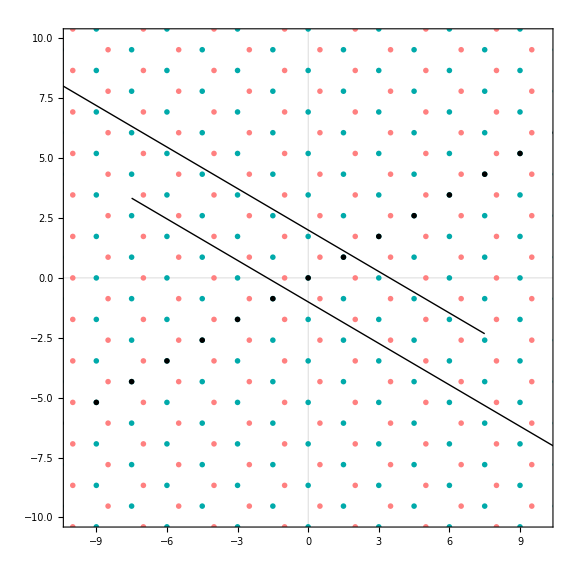

```mathematica
Show[{A,B,c,UCL,UCR(*,δvec,Avec,Bvec*)},PlotRange->(*Full*){{-10,10},{-10,10}},AspectRatio->1]
```

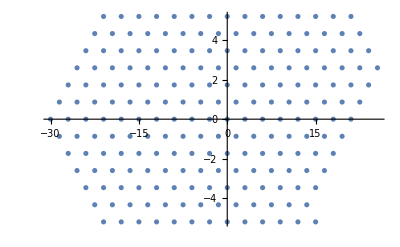

-Graphics-

```mathematica
EmptyListTest={};
Do[
Do[
If[Abs[Table[LatticeA[n,m],{n,-10,10,1},{m,-10,10,1}][[j]][[l]][[2]]]<6,AppendTo[EmptyListTest,Table[LatticeA[n,m],{n,-10,10,1},{m,-10,10,1}][[j]][[l]]]]
,{l,1,Length[Table[LatticeA[n,m],{n,-10,10,1},{m,-10,10,1}][[j]]]}]
,{j,1,Length[Table[LatticeA[n,m],{n,-10,10,1},{m,-10,10,1}]]}]
Table[LatticeA[n,m],{n,-10,10,1},{m,-10,10,1}][[1]]
```

$Aborted

{{-30,0},{-57/2,(√3)/2},{-27,√3},{-51/2,(3 √3)/2},{-24,2 √3},{-45/2,(5 √3)/2},{-21,3 √3},{-39/2,(7 √3)/2},{-18,4 √3},{-33/2,(9 √3)/2},{-15,5 √3},{-27/2,(11 √3)/2},{-12,6 √3},{-21/2,(13 √3)/2},{-9,7 √3},{-15/2,(15 √3)/2},{-6,8 √3},{-9/2,(17 √3)/2},{-3,9 √3},{-3/2,(19 √3)/2},{0,10 √3}}

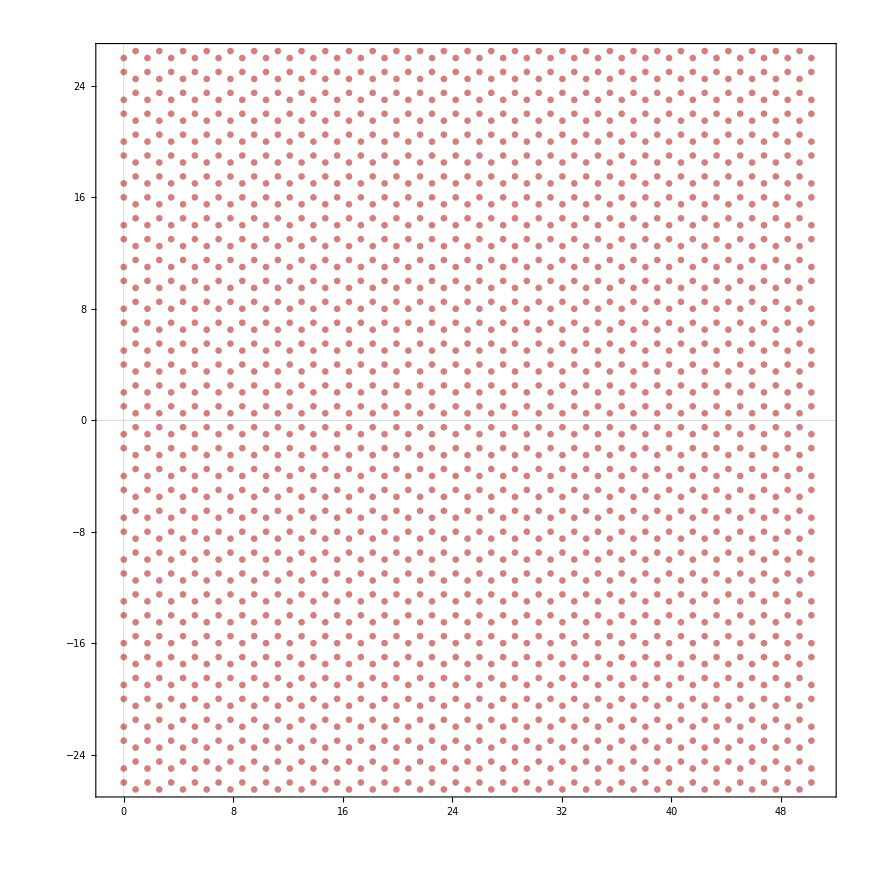

```mathematica
xpos=RecurrenceTable[{β[n+1]==β[n]+(√3)/2 KroneckerDelta[0,Mod[n,2]],β[1]==0},β,{n,1,2Num}];
ypos={-1,1,1/2,-1/2};
unitcell=Table[{xpos[[j]],ypos[[Mod[j-1,4]+1]]},{j,1,2Num}];
MANRlattice=Table[unitcell+Table[{0,3i},{j,1,2Num}],{i,-10,10}];
ListPlot[MANRlattice,Joined->False,PlotStyle->Directive[Darker[Red],Thick,Opacity[0.5]],
LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],PlotTheme->"Scientific",PlotRange->{{-1,51},{-26,26}},ImageSize->Large,AspectRatio->1]
```

## Parameter Definitions

### Lattice Parameters

```mathematica
a=4*10^-10(*m*);
J=2;
h=0.05;
J2=0.15;
s=3/2;
DM=0.3;
κ=0;
ϕ=ArcTan[DM/J2](*Pi/2*);
ℏ=6.582*10^-1; (*meV/THz*)
```

### Constants

```mathematica
kb=8.6*10^-2; (*meV*)

γe=1.76*10^11;(*rad*s^-1*T^-1*)
μ0=4Pi*10^-7;(*N/m^2*)
μB=9.274*10^-24 (*J*T^-1*);
Ms=(3/2 μB s)/(a^2 w);
w=10^-10;(*m*)
```

### Computational Settings

```mathematica
WP=60;
AG=10;
```

## MANR Dispersion

```mathematica
Naux=500;
Num=59;
Δκ=0;

Do[
ξ=-Pi/3+j* N[(2 Pi/3)/Naux];

H=MANRMatrix2N[J,J2,DM,s,0,Δκ,h,ϕ,ξ,Num];
sortorder=Ordering[Eigensystem[H][[1]]];

f[ξ]=Table[{ξ ,(Eigensystem[H][[1]][[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}];

,{j,0,Naux}]//AbsoluteTiming

p=ListPlot[Table[f[ξ],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",□FontSize->20}],FrameLabel->{"ka","ω (THz)"},PlotStyle->Directive[Black,Thickness[.01]],PlotRange->All,PlotTheme->"Scientific"];
```

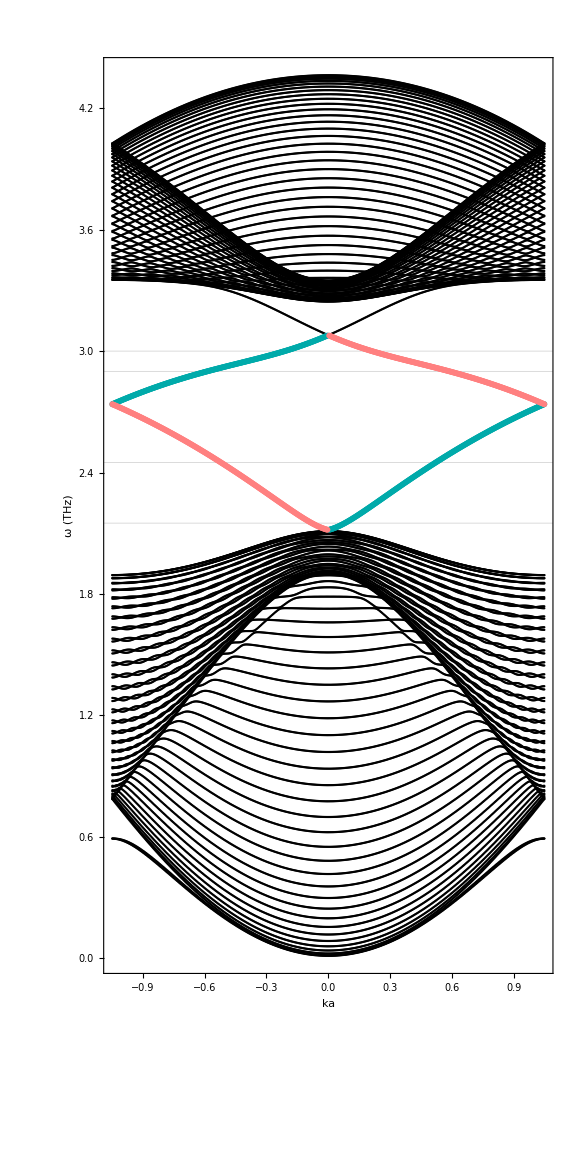

```mathematica
RightUpperBand=Select[Table[f[ξ][[Num+2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}],#[[1]]>0&];
RightLowerBand=Select[Table[f[ξ][[Num+1]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}],#[[1]]>0&];
LeftUpperBand=Select[Table[f[ξ][[Num+2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}],#[[1]]<0&];
LeftLowerBand=Select[Table[f[ξ][[Num+1]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}],#[[1]]<0&];
PositiveBand=Select[Join[LeftUpperBand,RightLowerBand],2<#[[2]]<3.2&];
NegativeBand=Select[Join[LeftLowerBand,RightUpperBand],2<#[[2]]<3.2&];
ppos=ListPlot[PositiveBand,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω (THz)"},PlotStyle->Directive[Darker[Cyan],Thickness[.01]],PlotRange->All,PlotTheme->"Scientific"];
pneg=ListPlot[NegativeBand,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω (THz)"},PlotStyle->Directive[Pink,Thickness[.01]],PlotRange->All,PlotTheme->"Scientific"];
(*pp=ListPlot[Table[f[ξ][[31]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω (THz)"},PlotStyle->Directive[Red,Thickness[.01]],PlotRange->All,PlotTheme->"Scientific"];
ppp=ListPlot[Table[f[ξ][[30]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω (THz)"},PlotStyle->Directive[Blue,Thickness[.01]],PlotRange->All,PlotTheme->"Scientific"];*)
Show[{p,ppos,pneg},ImageSize->Large,GridLines->{{},{2.15,2.45,2.9,3}},PlotRange->Full,AspectRatio->2]
```

### Pretty Picture

```mathematica
Naux=300;
Num=59;
κ=0.3;
Δκ=0.1;

Do[
ξ=-Pi/3+j* N[(2 Pi/3)/Naux];

H=MANRMatrix2N[J,J2,DM,s,κ,Δκ,h,ϕ,ξ,Num];

A=Eigensystem[H];

sortorder=Ordering[A[[1]]];

f[ξ]=Table[{ξ ,(A[[1]][[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}];

,{j,0,Naux}]
```

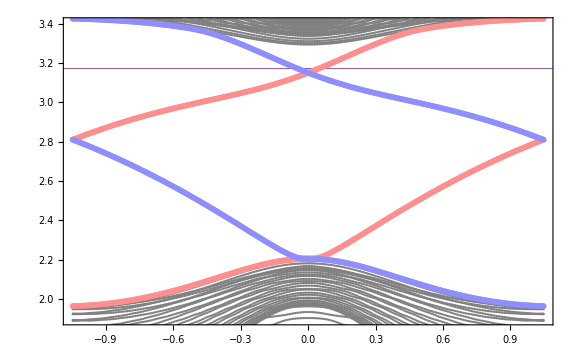

```mathematica
p4=ListPlot[Table[f[ξ],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}],LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotStyle->Directive[Gray],PlotRange->All,PlotTheme->"Scientific"];

RightUpperBand=Select[Table[f[ξ][[Num+2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}],#[[1]]>0&];
RightLowerBand=Select[Table[f[ξ][[Num+1]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}],#[[1]]>0&];
LeftUpperBand=Select[Table[f[ξ][[Num+2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}],#[[1]]<0&];
LeftLowerBand=Select[Table[f[ξ][[Num+1]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}],#[[1]]<0&];

LeftLowerLowerBand=Select[Table[f[ξ][[Num]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}],#[[1]]<0&];
LeftUpperUpperBand=Select[Table[f[ξ][[Num+3]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}],#[[1]]<0&];
RightLowerLowerBand=Select[Table[f[ξ][[Num]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}],#[[1]]>0&];
RightUpperUpperBand=Select[Table[f[ξ][[Num+3]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}],#[[1]]>0&];

PositiveBand=Select[Join[LeftUpperBand,RightLowerBand,LeftLowerLowerBand,RightUpperUpperBand],1.8+κ/(2Pi ℏ)<#[[2]]<3.4+κ/(2Pi ℏ)&];
NegativeBand=Select[Join[LeftLowerBand,RightUpperBand,LeftUpperUpperBand,RightLowerLowerBand],1.8+κ/(2Pi ℏ)<#[[2]]<3.4+κ/(2Pi ℏ)&];
ppos=ListPlot[PositiveBand,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],FrameLabel->{"k_ya","ω/2π (THz)"},PlotStyle->Directive[Lighter[Lighter[Red]],Thickness[.1]],PlotRange->All,PlotTheme->"Scientific"(*,PlotMarkers->{"●",Small}*)];
pneg=ListPlot[NegativeBand,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],FrameLabel->{"k_ya","ω/2π (THz)"},PlotStyle->Directive[Lighter[Lighter[Blue]],Thickness[.1]],PlotRange->All,PlotTheme->"Scientific"(*,PlotMarkers->{"●",Small}*)];
(*Show[p4,ImageSize->Full,(*GridLines->{{-0.5,0.5},{{2.9,Directive[Red,Thick]},{2.95,Directive[Orange,Thick]},{3,Directive[Yellow,Thick]},{3.05,Directive[Green,Thick]},{3.1,Directive[Blue,Thick]},{3.15,Directive[Magenta,Thick]},{3.2,Directive[Purple,Thick]}}}*)(*GridLines->{{},{{2.2,Directive[Darker[RGBColor["#ada132"]],Thickness[0.008],Opacity[0.75]]},{2.7,Directive[Darker[RGBColor["#789953"]],Thickness[0.008],Opacity[0.75]]},{3.2,Directive[Darker[RGBColor["#9f6dbe"]],Thickness[0.008],Opacity[0.75]]}}},Method->{"GridLinesInFront"->True},*)AspectRatio->1/GoldenRatio]*)
Show[p4,ppos,pneg,ImageSize->Large,GridLines->{{},{3.1+κ/(2Pi ℏ)}},GridLinesStyle->Directive[ColorData["GreenPinkTones",14/15],Thick],Method->{"GridLinesInFront"->True},PlotRange->{All,{1.9,3.4}},FrameStyle->Thick]
```

## MANR Wavefunctions

### Single Omega

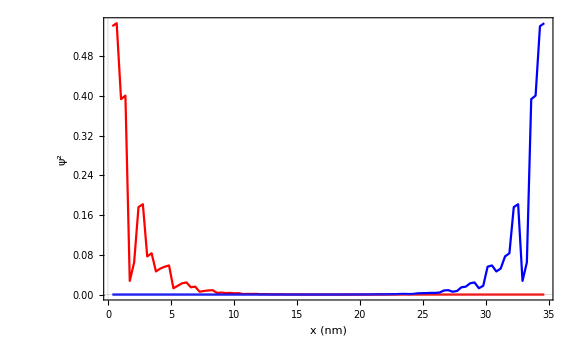

```mathematica
Num=50;
U1=UMatrix[J,J2,DM,s,κ,h,ϕ,0.3,Num];
fr=ListPlot[Table[{(√3)/2 0.4*M,Abs[U1[[Num]][[M]]]},{M,0,2Num}],PlotRange->All,Joined->True,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"x (nm)","ψ^2"},PlotStyle->Directive[Blue],PlotRange->All,PlotTheme->"Scientific"];
U2=UMatrix[J,J2,DM,s,κ,h,ϕ,-0.3,Num];
fl=ListPlot[Table[{(√3)/2 0.4*M,Abs[U2[[Num]][[M]]]},{M,0,2Num}],PlotRange->All,Joined->True,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"x (nm)","ψ^2"},PlotStyle->Directive[Red],PlotRange->All,PlotTheme->"Scientific"];
Show[{fl,fr},PlotRange->All,ImageSize->Large]
```

### Range of Omegas

```mathematica
Wavefunctions={};
Do[
Ul=UMatrix[J,J2,DM,s,κ,h,ϕ,PositiveBand[[j]][[1]],Num];
fl=Table[{(√3)/2 M *a/10^-9,Abs[U1[[Num+1]][[M]]]^2},{M,0,2Num}];
U2=UMatrix[J,J2,DM,s,κ,h,ϕ,Reverse[NegativeBand][[j]][[1]],Num];
fr=Table[{(√3)/2 M a/10^-9,Abs[U2[[Num+1]][[M]]]^2},{M,0,2Num}];
AppendTo[Wavefunctions,{fl,fr}]
,{j,1,Length[PositiveBand]}]
```

Part::partd: Part specification U1⟦31⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of U1⟦31⟧ does not exist.

Part::partw: Part 4 of U1⟦31⟧ does not exist.

Part::partw: Part 5 of U1⟦31⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

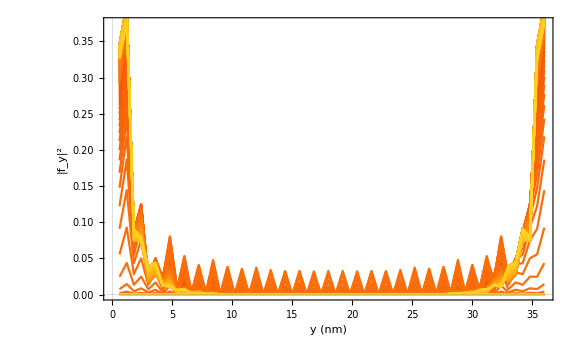

```mathematica
Show[Table[ListPlot[Wavefunctions[[j]],PlotRange->All,Joined->True,PlotStyle->ColorData["SolarColors",j/Length[Wavefunctions]],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"y (nm)","|f_y|^2"},PlotTheme->"Scientific"],{j,1,Length[Wavefunctions]}],ImageSize->Large]
```

### Algorithm

```mathematica
(*Calculate table of values*)
(*κ=0.3;
Δκ=0.05;*)

Naux=500;
Num=59;

upperbound=3.4;
lowerbound=1.8;

WaveAlgo[J_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,Num_,Naux_,upperbound_,lowerbound_]:=
Module[{N0=Num,NBand=Naux,A},

Do[
ξ=-Pi/3+j* N[(2 Pi/3)/Naux];

H=MANRMatrix2N[J,J2,DM,s,κ,Δκ,h,ϕ,ξ,Num];

A=Eigensystem[H];

sortorder=Ordering[A[[1]]];

f[ξ]=Table[{ξ ,(A[[1]][[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}];

,{j,0,Naux}];

(*Fun[l_]:=Table[f[ξ][[l]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}];*)

(*Iterates through table of values to grab indices which coincide to bands within desired bounds*)
FindIndices[NBand_,N0_,ub_,lb_]:=
Module[{EmptyList,Indices},
EmptyList={};

Do[
Do[
If[lb<Table[f[ξ][[i]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/NBand]}][[j]]<ub, AppendTo[EmptyList,i]]
,{j,1,Length[Table[f[ξ][[i]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/NBand]}]]}]
,{i,1,2N0}];

Indices=DeleteDuplicates[EmptyList];
Indices
];

BandIndices=FindIndices[Naux,Num,upperbound,lowerbound];

(*Find k value and corresponding band index for a fixed energy*)
FindMom[ω_,err_]:=
Module[{EmptyList,Mom},
EmptyList={};

Do[
Do[
If[ω-err<Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]]<ω+err, AppendTo[EmptyList,{BandIndices[[i]],Table[f[ξ][[BandIndices[[i]]]][[1]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]],Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]]}]]
,{j,1,Length[Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}]]}]
,{i,1,Length[BandIndices]}];

Mom=Sort[EmptyList,Abs[#1[[1]]]<Abs[#2[[1]]]&] (*Sorts list from smallest to largest absolute momentum*)
];

(*Takes the mean value of closely separated k values*)
MeanMom[ω_,err_]:=
Module[{MomList,DeleteMomList,EmptyList},

MomList=Split[FindMom[ω,err],Abs[#1[[2]]-#2[[2]]]<err&&#1[[1]]==#2[[1]]&];
EmptyList={};

For[i=1,i<Length[MomList]+1,i++,AppendTo[EmptyList,Mean[MomList[[i]]]]];

EmptyList
];

(*Calculates the wavefunction for impure spin lattice*)
(*NOTE: I changed the x recurrence table to sum in steps of 1/2 instead of √3/2*)
wavefunctions[ω_,err_,N0]:=
Module[{wavefunction,U,f,k,band,β,n,x},
wavefunction={};

Do[
k=MeanMom[ω,err][[j]][[2]];
band=MeanMom[ω,err][[j]][[1]];
U=UMatrix[J,J2,DM,s,κ,Δκ,h,ϕ,k,Num];
x=RecurrenceTable[{β[n+1]==β[n]+(√3)/2 KroneckerDelta[0,Mod[n,2]],β[1]==0},β,{n,1,2Num}];
f=Table[{x[[M]] *a/10^-9,Abs[U[[band]][[M]]]^2},{M,1,2Num}];
AppendTo[wavefunction,f]
,{j,1,Length[MeanMom[ω,err]]}];

wavefunction

];

];
```

### Plot spatial profile

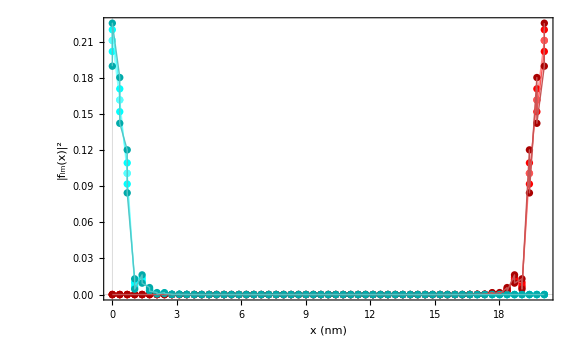

```mathematica
(*Plot that shit!*)

WaveTable = {};

Do[
Δκ=0+0.1(m-1);

WaveAlgo[J,J2,DM,s,κ,Δκ,h,ϕ,Num,Naux,upperbound,lowerbound];
Wavefunctions=wavefunctions[3.05,0.01,Num];

Colors={{Lighter[Red],Lighter[Cyan]},{Red,Cyan},{Darker[Red],Darker[Cyan]}};

wave[i_]:=Show[Table[ListPlot[Wavefunctions[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[Colors[[i]][[j]],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"x (nm)","|f_lm(x)|^2"},PlotTheme->"Scientific"],{j,1,Length[Wavefunctions]}],ImageSize->Large,PlotRange->All];

wavej[i_]:=Show[Table[ListPlot[Wavefunctions[[j]],PlotRange->All,Joined->True,PlotStyle->Directive[Lighter[Colors[[i]][[j]]],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"x (nm)","|f_lm(x)|^2"},PlotTheme->"Scientific"],{j,1,Length[Wavefunctions]}],ImageSize->Large,PlotRange->All];

AppendTo[WaveTable,{wave[m],wavej[m]}]

,{m,1,3}]

Show[WaveTable]
```

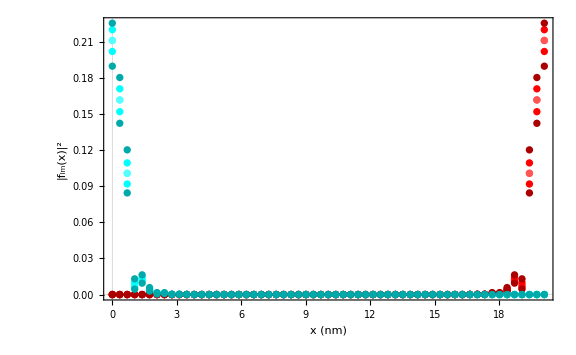

-Graphics-

```mathematica
Show[WaveTable[[1]][[1]],WaveTable[[2]][[1]],WaveTable[[3]][[1]]]
Show[WaveTable]
```

```mathematica
Clear[n,k,band];
(*k=MeanMom[3.1,0.01][[1]][[2]];
band=MeanMom[3.1,0.01][[1]][[1]];
x=RecurrenceTable[{β[n+1]==β[n]+(√3)/2 KroneckerDelta[0,Mod[n,2]],β[1]==0},β,{n,1,2Num}];
ListPlot[Table[{x[[M]] *a/10^-9,Abs[UMatrix[J,J2,DM,s,0.4,0,h,ϕ,k,Num][[band]][[M]]]^2},{M,1,2Num}],PlotRange->All,Joined->True]
ListPlot[Table[{x[[M]] *a/10^-9,Abs[UMatrix[J,J2,DM,s,0,0,h,ϕ,k,Num][[band]][[M]]]^2},{M,1,2Num}],PlotRange->All,Joined->True]*)
```

```mathematica
(*Export["MANR_spat_prof_omega=3.2.mx",Wavefunctions];*)

(*Uncomment the following to do a smooth interpolation of the spatial profile*)

(*TestEmptyList={};
Do[
Do[
AppendTo[TestEmptyList,Wavefunctions[[i]][[j]][[2]]]
,{j,1,Length[Wavefunctions[[i]]]}];
,{i,1,Length[Wavefunctions]}];*) 

(*TestEmptyList2={};
Do[
AppendTo[TestEmptyList2,{Wavefunctions[[1]][[j]][[1]],TestEmptyList[[1;;2Num ]][[j]]+TestEmptyList[[2Num+1;;4Num ]][[j]]}]
,{j,1,Length[Wavefunctions[[1]]]}]

Do[
v=ListInterpolation[TestEmptyList[[2Num*(j-1)+1;;2Num j]],{0,(3/2(Num)-1)*(0.4)}];
plot[j]=Plot[Abs[v[x]],{x,0,(3/2(Num)-1)*(0.4)},LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"y (nm)","|f_lm(y)|^2"},PlotStyle->Directive[Red,Thickness[0.005]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large]
,{j,1,Length[Wavefunctions]}];*)


(*wavecolors={{RGBColor["#07f738"],RGBColor["#e6a835"]},{RGBColor["#0aeb5a"],RGBColor["#eaa23a"]},{RGBColor["#07f78a"],RGBColor["#e69037"]},{RGBColor["#0beba9"],RGBColor["#e57e36"]},{RGBColor["#e67137"],RGBColor["#07f7db"]},{RGBColor["#f56438"],RGBColor["#08d9db"]},{RGBColor["#e65337"],RGBColor["#07c6f7"]},{RGBColor["#0584c7"],RGBColor["#e63741"]},{RGBColor["#077af7"],RGBColor["#ad352c"]}};*)
```

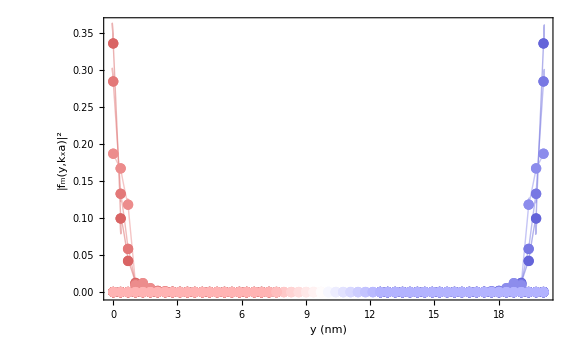

```mathematica
WaveAlgo[J,J2,DM,s,κ,0,h,ϕ,Num,100,upperbound,lowerbound];

Wavefunctions=ConstantArray[0,9];

Do[
ω=2.3+0.1*j;
Wavefunctions[[j]]=wavefunctions[ω,1/100,Num]
,{j,1,9}];


test1=Show[Table[ListPlot[Select[Wavefunctions,UnsameQ[#,{}]&][[j]][[2]][[;;Num-14]],PlotRange->All,Joined->False,PlotStyle->Directive[Blend[{Darker[Red],Lighter[Lighter[Lighter[Red]]]},j/Length[Select[Wavefunctions,UnsameQ[#,{}]&]]],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[Select[Wavefunctions,UnsameQ[#,{}]&]]}],ImageSize->Large,PlotRange->All];
test2=Show[Table[ListPlot[Select[Wavefunctions,UnsameQ[#,{}]&][[j]][[2]][[;;Num-14]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[Blend[{Darker[Red],Lighter[Lighter[Lighter[Red]]]},j/Length[Select[Wavefunctions,UnsameQ[#,{}]&]]],Opacity[0.5],Thick],
LabelStyle->Directive[Black,{FontFamily->"Cambria Math",FontSize->20}],FrameLabel->{"y (nm)","|f_m(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[Select[Wavefunctions,UnsameQ[#,{}]&]]}],ImageSize->Large,PlotRange->All];

test3=Show[Table[ListPlot[Select[Wavefunctions,UnsameQ[#,{}]&][[j]][[1]][[Num+14;;]],PlotRange->All,Joined->False,PlotStyle->Directive[Blend[{Darker[Blue],Lighter[Lighter[Lighter[Blue]]]},j/Length[Select[Wavefunctions,UnsameQ[#,{}]&]]],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[Select[Wavefunctions,UnsameQ[#,{}]&]]}],ImageSize->Large,PlotRange->All];
test4=Show[Table[ListPlot[Select[Wavefunctions,UnsameQ[#,{}]&][[j]][[1]][[Num+14;;]],PlotRange->All,Joined->True,InterpolationOrder->2,PlotStyle->Directive[Blend[{Darker[Blue],Lighter[Lighter[Lighter[Blue]]]},j/Length[Select[Wavefunctions,UnsameQ[#,{}]&]]],Opacity[0.5],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[Select[Wavefunctions,UnsameQ[#,{}]&]]}],ImageSize->Large,PlotRange->All];

ColorList=Table[Blend[{Blend[{Darker[Red],Lighter[Lighter[Lighter[Red]]]},1],White,Blend[{Darker[Blue],Lighter[Lighter[Lighter[Blue]]]},1]},j/Length[Select[Wavefunctions,UnsameQ[#,{}]&][[1]][[1]][[20;;48]]]],{j,1,Length[Select[Wavefunctions,UnsameQ[#,{}]&][[1]][[1]][[20;;48]]]}];

test5=Table[ListPlot[{Select[Wavefunctions,UnsameQ[#,{}]&][[1]][[1]][[Num-14;;Num+14]][[j]]},PlotRange->All,Joined->False,PlotStyle->Directive[ColorList[[j]],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific",ImageSize->Large],{j,1,Length[Select[Wavefunctions,UnsameQ[#,{}]&][[1]][[1]][[20;;48]]]}];

test6=Table[ListPlot[Partition[Select[Wavefunctions,UnsameQ[#,{}]&][[1]][[1]][[Num-14;;Num+14]],2][[j]],Joined->True,PlotRange->All,Joined->True,
PlotStyle->Directive[ColorList[[2j]],Opacity[0.5],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific",ImageSize->Large],{j,1,Length[Partition[Select[Wavefunctions,UnsameQ[#,{}]&][[1]][[1]][[20;;48]],2]]}];

Show[test2,test1,test4,test3,test6,test5,FrameStyle->Thick,GridLines->{}]
```

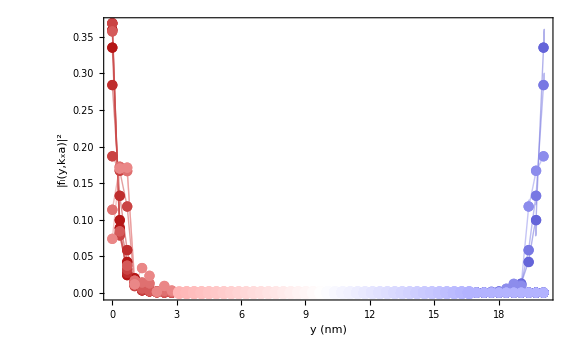

```mathematica
test1=Show[Union[Table[ListPlot[Select[Wavefunctions,#[[1]][[1]][[2]]==0&][[j]][[2]][[;;20]],PlotRange->All,Joined->False,PlotStyle->Directive[Blend[{Darker[Red],Lighter[Lighter[Lighter[Red]]]},j/8],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[Select[Wavefunctions,#[[1]][[1]][[2]]==0&]]}],Table[ListPlot[Select[Wavefunctions,#[[1]][[1]][[2]]!=0&][[j]][[1]][[;;20]],PlotRange->All,Joined->False,PlotStyle->Directive[Blend[{Darker[Red],Lighter[Lighter[Lighter[Red]]]},j/8],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[Select[Wavefunctions,#[[1]][[1]][[2]]!=0&]]}]
],PlotRange->All];
test2=Show[Union[Table[ListPlot[Select[Wavefunctions,#[[1]][[1]][[2]]==0&][[j]][[2]][[;;20]],PlotRange->All,Joined->True,PlotStyle->Directive[Blend[{Darker[Red],Lighter[Lighter[Lighter[Red]]]},j/8],Opacity[0.5],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[Select[Wavefunctions,#[[1]][[1]][[2]]==0&]]}],Table[ListPlot[Select[Wavefunctions,#[[1]][[1]][[2]]!=0&][[j]][[1]][[;;20]],PlotRange->All,Joined->True,PlotStyle->Directive[Blend[{Darker[Red],Lighter[Lighter[Lighter[Red]]]},j/8],Opacity[0.5],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[Select[Wavefunctions,#[[1]][[1]][[2]]!=0&]]}]
],PlotRange->All];

test3=Show[Table[ListPlot[Select[Wavefunctions,UnsameQ[#,{}]&][[j]][[1]][[Num+14;;]],PlotRange->All,Joined->False,PlotStyle->Directive[Blend[{Darker[Blue],Lighter[Lighter[Lighter[Blue]]]},j/Length[Select[Wavefunctions,UnsameQ[#,{}]&]]],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[Select[Wavefunctions,UnsameQ[#,{}]&]]}],ImageSize->Large,PlotRange->All];
test4=Show[Table[ListPlot[Select[Wavefunctions,UnsameQ[#,{}]&][[j]][[1]][[Num+14;;]],PlotRange->All,Joined->True,InterpolationOrder->2,PlotStyle->Directive[Blend[{Darker[Blue],Lighter[Lighter[Lighter[Blue]]]},j/Length[Select[Wavefunctions,UnsameQ[#,{}]&]]],Opacity[0.5],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[Select[Wavefunctions,UnsameQ[#,{}]&]]}],ImageSize->Large,PlotRange->All];

ColorList=Table[Blend[{Blend[{Darker[Red],Lighter[Lighter[Lighter[Red]]]},1],White,Blend[{Darker[Blue],Lighter[Lighter[Lighter[Blue]]]},1]},j/Length[Select[Wavefunctions,UnsameQ[#,{}]&][[1]][[1]][[20;;98]]]],{j,1,Length[Select[Wavefunctions,UnsameQ[#,{}]&][[1]][[1]][[20;;98]]]}];

test5=Table[ListPlot[{Select[Wavefunctions,UnsameQ[#,{}]&][[1]][[1]][[20;;98]][[j]]},PlotRange->All,Joined->False,PlotStyle->Directive[ColorList[[j]],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific",ImageSize->Large,PlotMarkers->{"●",Medium}],{j,1,Length[Select[Wavefunctions,UnsameQ[#,{}]&][[1]][[1]][[20;;98]]]}];

test6=Table[ListPlot[Partition[Select[Wavefunctions,UnsameQ[#,{}]&][[1]][[1]][[20;;98]],2][[j]],Joined->True,PlotRange->All,Joined->True,
PlotStyle->Directive[ColorList[[2j]],Opacity[0.5],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific",ImageSize->Large],{j,1,Length[Partition[Select[Wavefunctions,UnsameQ[#,{}]&][[1]][[1]][[20;;98]],2]]}];

Show[test2,test1,test4,test3,test6,test5,FrameStyle->Thick,GridLines->{},ImageSize->Large]
```

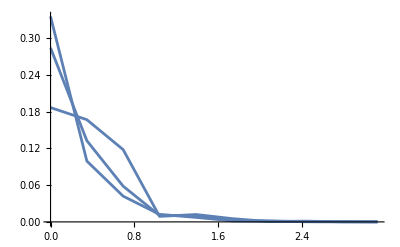

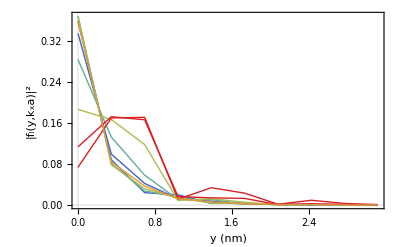

```mathematica
Show[Table[ListPlot[Select[Wavefunctions,#[[1]][[1]][[2]]==0&][[j]][[2]][[;;20]],PlotRange->All,Joined->True],{j,1,Length[Select[Wavefunctions,#[[1]][[1]][[2]]==0&]]}]]
Show[Union[Table[ListPlot[Select[Wavefunctions,#[[1]][[1]][[2]]==0&][[j]][[2]][[;;20]],PlotRange->All,Joined->True,PlotStyle->Directive[ColorData["Rainbow",j/5],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[Select[Wavefunctions,#[[1]][[1]][[2]]==0&]]}],Table[ListPlot[Select[Wavefunctions,#[[1]][[1]][[2]]!=0&][[j]][[1]][[;;20]],PlotRange->All,Joined->True,PlotStyle->Directive[ColorData["Rainbow",j/5],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[Select[Wavefunctions,#[[1]][[1]][[2]]!=0&]]}]
],PlotRange->All]
```

```mathematica
Length[Union[Table[ListPlot[Select[Wavefunctions,#[[1]][[1]][[2]]==0&][[j]][[2]][[;;20]],PlotRange->All,Joined->True],{j,1,Length[Select[Wavefunctions,#[[1]][[1]][[2]]==0&]]}],Table[ListPlot[Select[Wavefunctions,#[[1]][[1]][[2]]!=0&][[j]][[1]][[;;20]],PlotRange->All,Joined->True],{j,1,Length[Select[Wavefunctions,#[[1]][[1]][[2]]!=0&]]}]
]]
```

9

```mathematica
PlotList=Union[Table[ListPlot[Select[Wavefunctions,#[[1]][[1]][[2]]==0&][[j]][[2]][[;;20]],PlotRange->All,Joined->True,PlotStyle->Directive[ColorData["Rainbow",j/5],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[Select[Wavefunctions,#[[1]][[1]][[2]]==0&]]}],Table[ListPlot[Select[Wavefunctions,#[[1]][[1]][[2]]!=0&][[j]][[1]][[;;20]],PlotRange->All,Joined->True,PlotStyle->Directive[ColorData["Rainbow",j/5],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[Select[Wavefunctions,#[[1]][[1]][[2]]!=0&]]}]
];
```

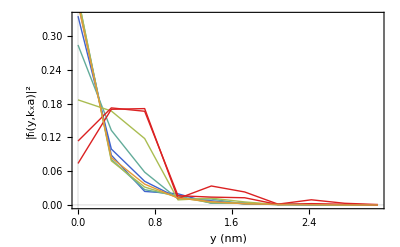

```mathematica
Show[PlotList]
```

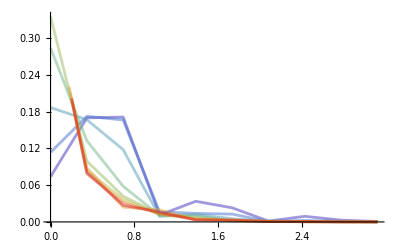

```mathematica
SpatProf1[j_]:=Select[Wavefunctions,#[[1]][[1]][[2]]==0&][[j]][[2]][[;;20]];
SpatProf2[j_]:=Select[Wavefunctions,#[[1]][[1]][[2]]!=0&][[j]][[1]][[;;20]];
SpatProf=Union[Table[SpatProf1[j],{j,1,3}],Table[SpatProf2[j],{j,1,6}]];
Sort[SpatProf,#1[[1]]>#2[[2]]&];
Show[Table[ListPlot[Sort[SpatProf,#1[[1]]>#2[[2]]&][[j]],PlotStyle->Directive[ColorData["Rainbow",j/9],Opacity[0.5]],Joined->True],{j,1,9}],PlotRange->All]
```

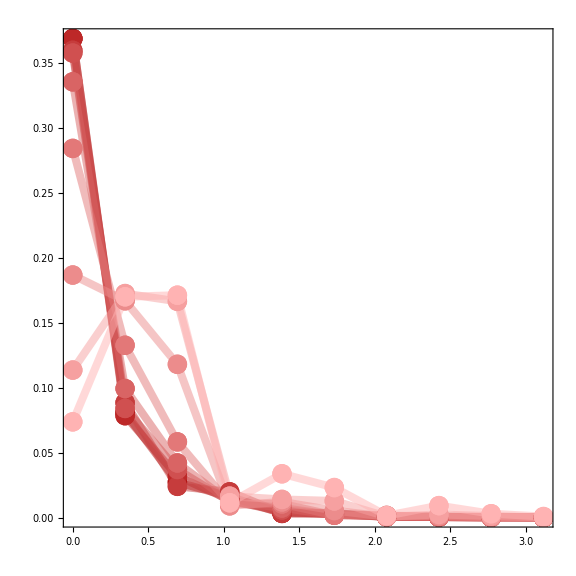

```mathematica
Colors=Table[Blend[{Darker[Red],Lighter[Lighter[Lighter[Red]]]},j/9],{j,1,9}];
test7=Table[ListPlot[Reverse[Sort[SpatProf,#1[[1]]<#2[[2]]&]][[j]],Joined->False,PlotRange->All,PlotStyle->Directive[{Colors[[j]]},Thick],LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific",PlotMarkers->{"●",Large}],{j,1,9}];
test8=Table[ListPlot[Reverse[Sort[SpatProf,#1[[1]]<#2[[2]]&]][[j]],Joined->True,PlotRange->All,PlotStyle->Directive[{Colors[[j]]},Opacity[0.5],Thickness[0.01]],LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"x (nm)","|f_m(x,k_ya)|^2"},PlotTheme->"Scientific"],{j,1,9}];
Show[test8,test7,PlotRange->All,ImageSize->Large,AspectRatio->1,FrameStyle->Directive[Thickness[0.01],FontSize->48],FrameLabel->{},GridLines->{}]
```

```mathematica
SpatProf3[j_]:=Select[Wavefunctions,#[[1]][[1]][[2]]!=0&][[j]][[2]][[98;;]];
SpatProf4[j_]:=Select[Wavefunctions,#[[1]][[1]][[2]]==0&][[j]][[1]][[98;;]];
SpatProf5=Union[Table[SpatProf3[j],{j,1,6}],Table[SpatProf4[j],{j,1,3}]];
Sort[SpatProf5,#1[[1]]>#2[[2]]&];
```

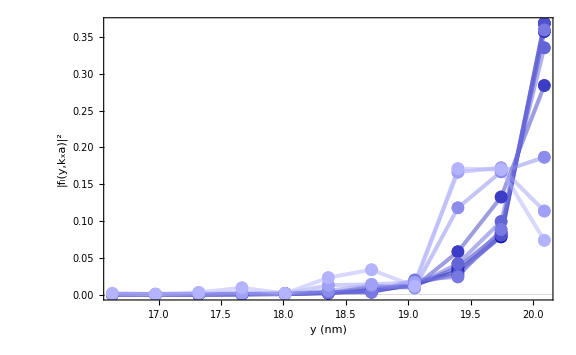

```mathematica
Colors2=Table[Blend[{Darker[Blue],Lighter[Lighter[Lighter[Blue]]]},j/9],{j,1,9}];
test9=Table[ListPlot[Reverse[Sort[SpatProf5,#1[[1]]>#2[[2]]&][[j]]],Joined->False,PlotRange->All,PlotStyle->Directive[{Colors2[[j]]},Thick],LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific",PlotMarkers->{"●",Medium}],{j,1,9}];
test10=Table[ListPlot[Reverse[Sort[SpatProf5,#1[[1]]>#2[[2]]&][[j]]],Joined->True,PlotRange->All,PlotStyle->Directive[{Colors2[[j]]},Opacity[0.5],Thickness[0.005]],LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,9}];
Show[test10,test9,PlotRange->All,ImageSize->Large]
```

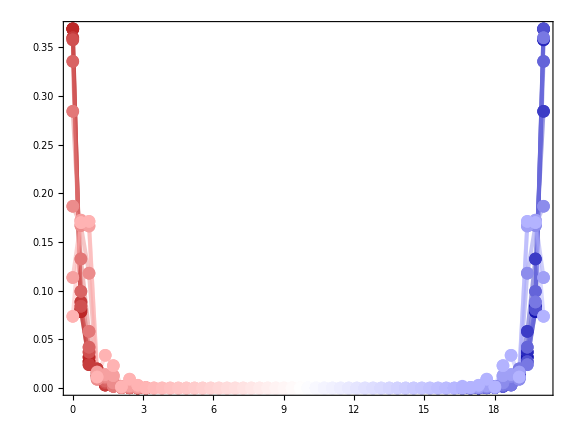

```mathematica
Show[test8,test7,test10,test9,test6,test5,PlotRange->All,ImageSize->Large,FrameStyle->Directive[Thickness[0.007],FontSize->36],GridLines->{},AspectRatio->3/4,FrameLabel->{}]
```

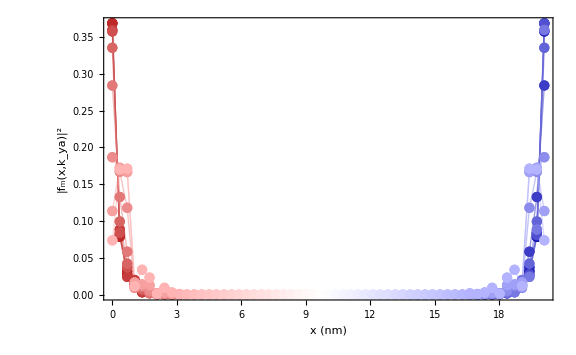
```mathematica
Show[-Graphics-,FrameLabel->{},AspectRatio->3/4,FrameStyle->Directive[Thickness[0.007],FontSize->42]]
```

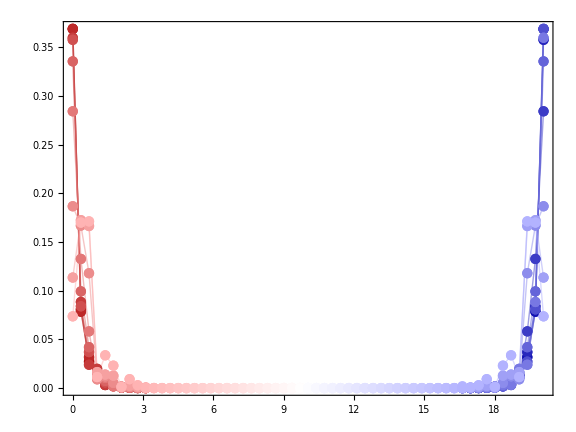

### Magnetization

```mathematica
BulkMagnetization[ω_,err_,Num_]:=
Module[{magx,magy,magx2,magy2,U,mx,my,mx2,my2,k,band,β,n,x,ypos},
magx={};
magy={};
magx2={};
magy2={};
ypos={-1,1,1/2,-1/2};

Do[
k=MeanMom[ω,err][[j]][[2]];
band=MeanMom[ω,err][[j]][[1]];
U=UMatrix[J,J2,DM,s,κ,Δκ,h,ϕ,k,Num];
x=RecurrenceTable[{β[n+1]==β[n]+(√3)/2 KroneckerDelta[0,Mod[n,2]],β[1]==0},β,{n,1,2Num}];
mx=Table[{x[[M]] *a/10^-9,(U[[band]][[M]] E^(-ⅈ k ypos[[Mod[M-1,4]+1]])+Conjugate[U[[band]][[M]] E^(-ⅈ k ypos[[Mod[M-1,4]+1]])])/2},{M,1,2Num}];
mx2=Table[{M,(U[[band]][[M]] E^(-ⅈ k ypos[[Mod[M-1,4]+1]])+Conjugate[U[[band]][[M]] E^(-ⅈ k ypos[[Mod[M-1,4]+1]])])/2},{M,1,2Num}];
my=Table[{x[[M]] *a/10^-9,ⅈ(U[[band]][[M]] E^(-ⅈ k ypos[[Mod[M-1,4]+1]])-Conjugate[U[[band]][[M]] E^(-ⅈ k ypos[[Mod[M-1,4]+1]])])/2},{M,1,2Num}];
my2=Table[{M,ⅈ(U[[band]][[M]] E^(-ⅈ k ypos[[Mod[M-1,4]+1]])-Conjugate[U[[band]][[M]] E^(-ⅈ k ypos[[Mod[M-1,4]+1]])])/2},{M,1,2Num}];
AppendTo[magx,mx];
AppendTo[magy,my];
AppendTo[magx2,mx2];
AppendTo[magy2,my2];
,{j,1,Length[MeanMom[ω,err]]}];

{magx,magy,magx2,magy2}

];
```

```mathematica
(*BM=BulkMagnetization[3.15,0.01,Num];
xmag=BM[[1]];
(*Export["MANR_magx_omega=2.7.mx",xmag];*)
ymag=BM[[2]];*)
(*Export["MANR_magy_omega=2.7.mx",ymag];*)
(*xmag2=BM[[3]];
Export["MANR_magx2_omega=2.7.mx",xmag];
ymag2=BM[[4]];
Export["MANR_magy2_omega=2.7.mx",ymag];*)
```

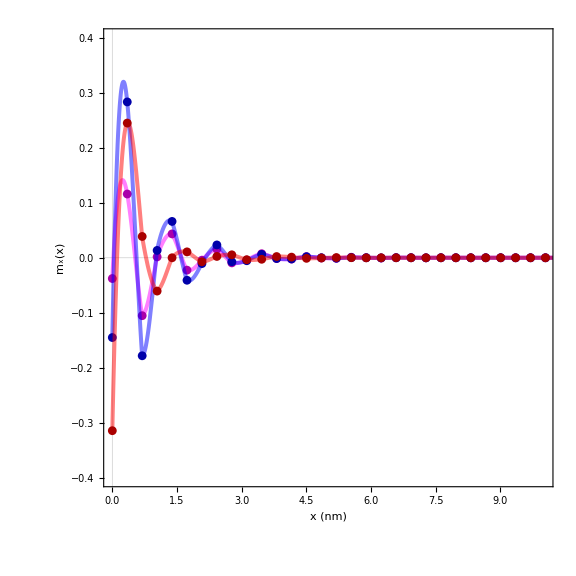

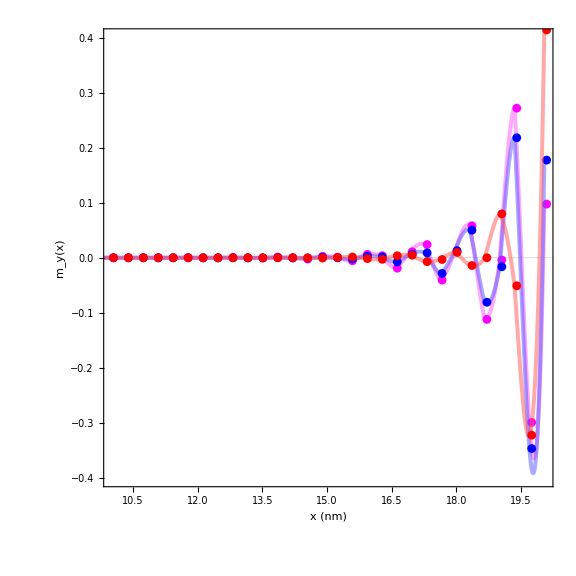

```mathematica
(*Show[Table[ListPlot[xmag[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[RGBColor["#789953"],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],FrameLabel->{"x (nm)","M_x(x)"},PlotTheme->"Scientific"],{j,1,Length[xmag]}],ImageSize->Large,PlotRange->All]
ListPlot[xmag[[1]],PlotRange->All]*)

xAvg={};
Do[
Do[
AppendTo[xAvg,Mean[Split[xmag[[l]],#1[[1]]==#2[[1]]&][[j]]]]
,{j,1,Length[Split[xmag[[l]],#1[[1]]==#2[[1]]&]]}]
,{l,1,Length[xmag]}]
xmagAvg=Table[{xAvg[[1;;Num]][[j]][[1]],xAvg[[1;;Num]][[j]][[2]]+xAvg[[Num+1;;2Num]][[j]][[2]]},{j,1,Length[xAvg[[1;;Num]]]}];

yAvg={};
Do[
Do[
AppendTo[yAvg,Mean[Split[ymag[[l]],#1[[1]]==#2[[1]]&][[j]]]]
,{j,1,Length[Split[ymag[[l]],#1[[1]]==#2[[1]]&]]}]
,{l,1,Length[ymag]}]
ymagAvg=Table[{yAvg[[1;;Num]][[j]][[1]],yAvg[[1;;Num]][[j]][[2]]+yAvg[[Num+1;;2Num]][[j]][[2]]},{j,1,Length[yAvg[[1;;Num]]]}];

magx6=ListPlot[xmagAvg,PlotRange->All,Joined->False,PlotStyle->Directive[Darker[Magenta],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"x (nm)",""},PlotTheme->"Scientific",ImageSize->Large];
magy6=ListPlot[ymagAvg,PlotRange->All,Joined->False,PlotStyle->Directive[Magenta,Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"x (nm)",""},PlotTheme->"Scientific",ImageSize->Large];

TestEmptyListy={};
Do[
AppendTo[TestEmptyListy,ymagAvg[[j]][[2]]]
,{j,1,Length[ymagAvg]}]

vy=ListInterpolation[TestEmptyListy,{0,((√3)/2(Num)-1)*(0.4)}];
magy61=Plot[vy[x],{x,0,((√3)/2(Num)-1)*(0.4)},LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->28}],FrameLabel->{"x (nm)","m_y(x)"},PlotStyle->Directive[Lighter[Magenta],Thickness[0.005],Opacity[0.5]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,FrameStyle->Directive[Thick]];

TestEmptyListx={};
Do[
AppendTo[TestEmptyListx,xmagAvg[[j]][[2]]]
,{j,1,Length[xmagAvg]}]

vx=ListInterpolation[TestEmptyListx,{0,((√3)/2(Num)-1)*(0.4)}];
magx61=Plot[vx[x],{x,0,((√3)/2(Num)-1)*(0.4)},LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->28}],FrameLabel->{"x (nm)","m_x(x)"},PlotStyle->Directive[Magenta,Thickness[0.005],Opacity[0.5]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,FrameStyle->Directive[Thick]];

Show[magx61,magx6,(*magx21,magx2,*)(*magx31,magx3,*)magx41,magx4,(*magx51,magx5,*)magx11,magx1,AspectRatio->1,PlotRange->{{0,((√3)/2(Num)-1)*(0.4)/2},{-0.4,0.4}}]
Show[magy61,magy6,(*magy21,magy2,*)(*magy31,magy3,*)magy41,magy4,(*magy51,magy5,*)magy11,magy1,AspectRatio->1,PlotRange->{{((√3)/2(Num)-1)*(0.4)/2,((√3)/2(Num)-1)*(0.4)},{-0.4,0.4}}]

(*Plot[vy[x]+vx[x],{x,0,((√3)/2(Num)-1)*(0.4)},LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"x (nm)","m_x(x)"},PlotStyle->Directive[Lighter[RGBColor["#789953"]],Thickness[0.005]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large]*)
```

```mathematica
(*MeanMom[2.15,0.01]
MeanMom[2.2,0.01]
MeanMom[2.25,0.01]
MeanMom[2.3,0.01]
MeanMom[2.35,0.01]
MeanMom[2.4,0.01]
MeanMom[2.9,0.01]
MeanMom[2.95,0.01]
MeanMom[3,0.01]
MeanMom[3.05,0.01]
MeanMom[3.1,0.01]
MeanMom[3.15,0.01]*)
(*ky=MeanMom[2.2,0.01][[1]][[2]];
DensityPlot[vx[x]*Cos[ky y]HeavisideTheta[x]HeavisideTheta[((√3)/2(Num)-1)*(0.4)-x],{x,-5,25},{y,0,5},PlotRange->All,MaxRecursion->15]
DensityPlot[vy[x]*Sin[ky y]HeavisideTheta[x]HeavisideTheta[((√3)/2(Num)-1)*(0.4)-x],{x,-5,25},{y,0,5},PlotRange->All,MaxRecursion->15]
VectorDensityPlot[{vx[x]*Cos[ky y]HeavisideTheta[x]HeavisideTheta[((√3)/2(Num)-1)*(0.4)-x],vy[x]*Sin[ky y]HeavisideTheta[x]HeavisideTheta[((√3)/2(Num)-1)*(0.4)-x]},{x,-5,25},{y,0,5},PlotRange->All,MaxRecursion->15]*)
```

5.29575×10^6

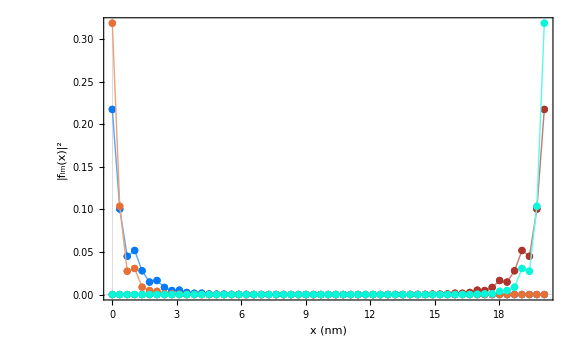

```mathematica
(*Plot that shit!*)

Wavefunctions=wavefunctions[2.25,0.01,Num];
(*Export["MANR_spat_prof_omega=3.2.mx",Wavefunctions];*)

TestEmptyList={};
Do[
Do[
AppendTo[TestEmptyList,Wavefunctions[[i]][[j]][[2]]]
,{j,1,Length[Wavefunctions[[i]]]}];
,{i,1,Length[Wavefunctions]}];

Colors={Darker[Red],Darker[Cyan]};

TestEmptyList2={};
Do[
AppendTo[TestEmptyList2,{Wavefunctions[[1]][[j]][[1]],TestEmptyList[[1;;2Num ]][[j]]+TestEmptyList[[2Num+1;;4Num ]][[j]]}]
,{j,1,Length[Wavefunctions[[1]]]}]

Do[
v=ListInterpolation[TestEmptyList[[2Num*(j-1)+1;;2Num j]],{0,(3/2(Num)-1)*(0.4)}];
plot[j]=Plot[Abs[v[x]],{x,0,(3/2(Num)-1)*(0.4)},LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"y (nm)","|f_lm(y)|^2"},PlotStyle->Directive[Red,Thickness[0.005]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large]
,{j,1,Length[Wavefunctions]}];


wavecolors={{RGBColor["#07f738"],RGBColor["#e6a835"]},{RGBColor["#0aeb5a"],RGBColor["#eaa23a"]},{RGBColor["#07f78a"],RGBColor["#e69037"]},{RGBColor["#0beba9"],RGBColor["#e57e36"]},{RGBColor["#e67137"],RGBColor["#07f7db"]},{RGBColor["#f56438"],RGBColor["#08d9db"]},{RGBColor["#e65337"],RGBColor["#07c6f7"]},{RGBColor["#0584c7"],RGBColor["#e63741"]},{RGBColor["#077af7"],RGBColor["#ad352c"]}};

wave2=Show[Table[ListPlot[Wavefunctions[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[wavecolors[[5]][[j]],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"x (nm)","|f_lm(x)|^2"},PlotTheme->"Scientific"],{j,1,Length[Wavefunctions]}],ImageSize->Large,PlotRange->All];

wave21=Show[Table[ListPlot[Wavefunctions[[j]],PlotRange->All,Joined->True,PlotStyle->Directive[Lighter[wavecolors[[5]][[j]]],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"x (nm)","|f_lm(x)|^2"},PlotTheme->"Scientific"],{j,1,Length[Wavefunctions]}],ImageSize->Large,PlotRange->All];

(*magx2=Show[Table[ListPlot[xmag[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[RGBColor["#789953"],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],FrameLabel->{"x (nm)","M_x(x)"},PlotTheme->"Scientific"],{j,1,Length[xmag]}],ImageSize->Large,PlotRange->All];

magx21=Show[Table[ListPlot[xmag[[j]],PlotRange->All,Joined->True,PlotStyle->Directive[Lighter[RGBColor["#789953"]],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],FrameLabel->{"x (nm)","M_x(x)"},PlotTheme->"Scientific"],{j,1,Length[xmag]}],ImageSize->Large,PlotRange->All];

magy2=Show[Table[ListPlot[ymag[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[RGBColor["#789953"],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],FrameLabel->{"x (nm)","M_y(x)"},PlotTheme->"Scientific"],{j,1,Length[ymag]}],ImageSize->Large,PlotRange->All];

magy21=Show[Table[ListPlot[ymag[[j]],PlotRange->All,Joined->True,PlotStyle->Directive[Lighter[RGBColor["#789953"]],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],FrameLabel->{"x (nm)","M_y(x)"},PlotTheme->"Scientific"],{j,1,Length[ymag]}],ImageSize->Large,PlotRange->All];*)
Show[wave11,wave1,wave21,wave2]
```

## Coupling

### Old

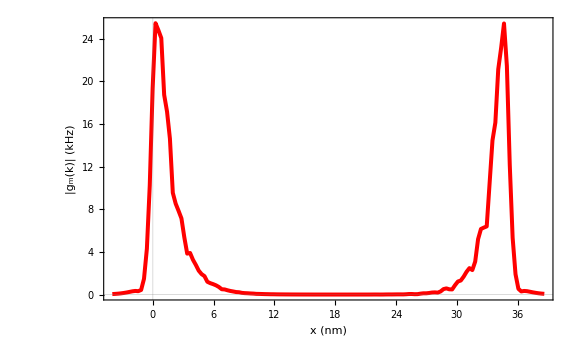

```mathematica
NSteps=150;

Num=50;
l=(√3)/2 2*Num*a;
d=2;
F=γe*μ0*√((3μB Ms)/(2l w))*10^-3; (*KHz*)


Quiet[
Do[
x=-10+j*N[(l/a+20)/NSteps];
(*FIXED ENERGY*)
gx=F*(MANRCoupling[J,J2,DM,s,κ,h,ϕ,-0.33,Num,Num+1,x,0,d]+MANRCoupling[J,J2,DM,s,κ,h,ϕ,0.33,Num,Num+1,x,0,d]);
gm[x]={0.4*x,gx};
,{j,0,NSteps}];

];
cplot4=ListPlot[Table[gm[x],{x,-10,l/a+10,N[(l/a+20)/NSteps]}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"x (nm)","|g_m(k)| (kHz)"},PlotStyle->Directive[Red,Thickness[.005]],PlotRange->All,PlotTheme->"Scientific",Joined-> True];

Show[cplot4,PlotRange->All,ImageSize->Large]
```

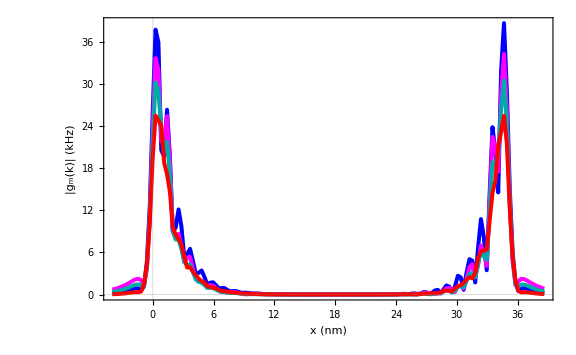

```mathematica
Show[{cplot1,cplot2,cplot3,cplot4},PlotRange->All,ImageSize->Large]
```

### Single Edge

### Full Strip

```mathematica
Δκ=0;
κ=0;
WaveAlgo[J,J2,DM,s,κ,Δκ,h,ϕ,Num,Naux,upperbound,lowerbound];

(*NOTE: to avoid any computational inaccuracy effects (i.e. non-mirror symmetric coupling profiles), make sure that NStep divides Num*)

NSteps=59;
Num=59;
ω=2.15+κ/(2Pi ℏ);
error=0.01;

l=((√3)/2*(Num-1))*a;
(*l=3/2*2*Num*a;*)
d=12.5;
F=γe/(2Pi)*μ0/(√a)*√((3μB Ms)/(2l w))*10^-3; (*kHz*)
```

```mathematica
Timing[numba=MeanMom[ω,error][[1]][[1]]]
Timing[mom=MeanMom[ω,error][[2]][[2]]]
Timing[F*MANRCouplingDiscrete[J,J2,DM,s,κ,Δκ,h,ϕ,mom,Num,numba,0,0,d,-3*200,3*200]]
```

{11.1875,60}

{10.9531,-0.079587}

{2.39063,3.84651}

```mathematica
CouplingList={};

Do[
numba=MeanMom[ω,error][[j]][[1]];
mom=MeanMom[ω,error][[j]][[2]];
Do[
x=-20+j*N[(l/a+40)/NSteps];
y=0;
gx=F*MANRCouplingDiscrete[J,J2,DM,s,κ,Δκ,h,ϕ,mom,Num,numba,x,y,d,-3*200,3*200];
gm[x]={0.4*x,gx};
,{j,0,NSteps}];

AppendTo[CouplingList,Table[gm[x],{x,-20,l/a+20,N[(l/a+40)/NSteps]}]];

,{j,1,Length[MeanMom[ω,error]]}];
(*
Export["MANR-SCQ_full_strip_omega=3.1.mx",CouplingList];*)
```

MANR-SCQ_full_strip_omega=2.15_V2.mx

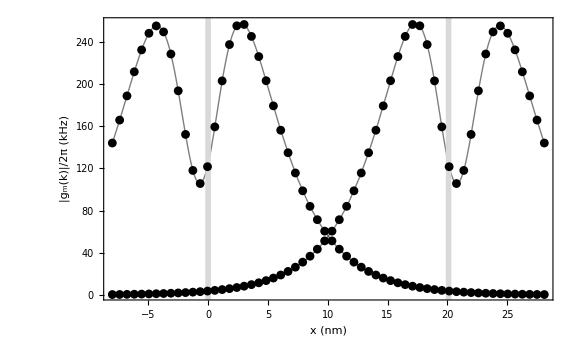

```mathematica
Colors={{Lighter[Red],Lighter[Red]},{Red,Red},{Darker[Red],Darker[Red]}};

Export["MANR-SCQ_full_strip_omega=2.15_V2.mx",CouplingList]

(*CouplingList=Import["MANR-SCQ_full_strip_omega=2.15.mx"];*)
cplot[i_]:=Show[Table[ListPlot[CouplingList[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[Black,Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"],{j,1,Length[CouplingList]}],ImageSize->Large,PlotRange->All,AspectRatio->1];

cplotsm[i_]:=Module[{TestEmptyList,v,plots},
TestEmptyList={};
Do[
Do[
AppendTo[TestEmptyList,CouplingList[[k]][[j]][[2]]]
,{j,1,Length[CouplingList[[k]]]}];
,{k,1,Length[CouplingList]}];

Do[

v=ListInterpolation[TestEmptyList[[Length[CouplingList[[j]]]*(j-1)+1;;Length[CouplingList[[j]]]*j]],{-8,N[l/a+20]*0.4}];
plot[j]=Plot[v[x],{x,-8,N[l/a+20]*0.4},LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"x (nm)","|g_m(k)|/2π (kHz)"},PlotStyle->Directive[Black,Thick,Opacity[0.5]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,PlotLegends->Automatic]
,{j,1,Length[CouplingList]}];

plots=Show[Table[plot[j],{j,1,Length[CouplingList]}],ImageSize->Large,PlotRange->All,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]]];
plots

];

MANRK1=cplot[1];
MANRK1sm=cplotsm[1];
Show[(*MANRK3sm,MANRK3,MANRK2sm,MANRK2,*)MANRK1sm,MANRK1,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]](*,PlotRange->{All,{0,475}}*)]
```

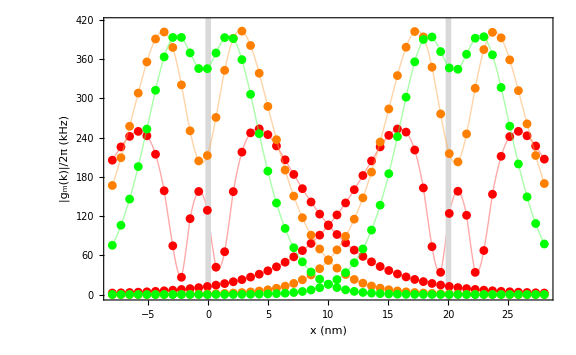

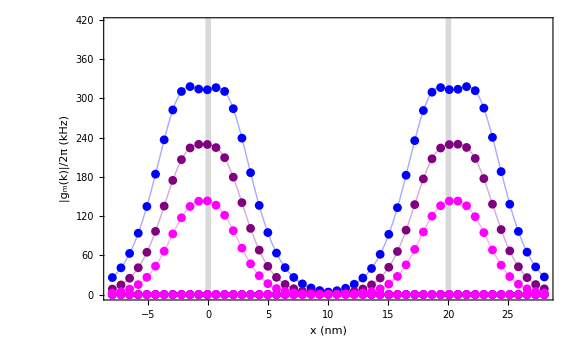

```mathematica
(*Show[w71,w7,w81,w8,w91,w9,w101,w10,w1111,w111,w121,w12]
Show[w71,w7,w91,w9,w1111,w111]
Show[w81,w8,w101,w10,w121,w12]*)
Show[w71,w7,w81,w8,w91,w9,PlotRange->{All,{0,415}}]
Show[w101,w10,w1111,w111,w121,w12,PlotRange->{All,{0,415}}]
```

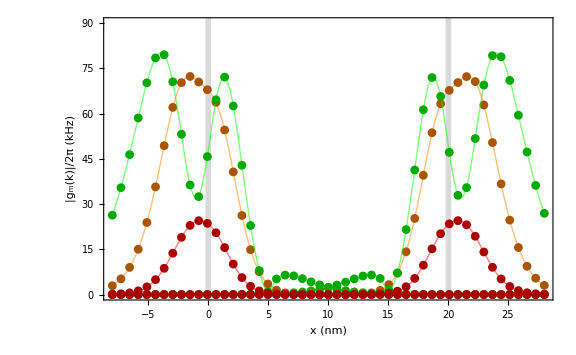

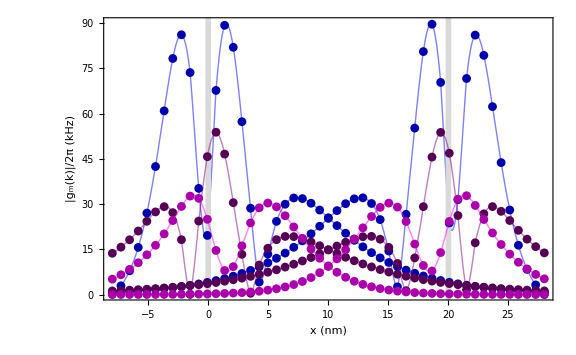

```mathematica
Show[w21,w2,w31,w3,w11,w1,AspectRatio->1/GoldenRatio,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],PlotRange->{All,{0,90}}]
Show[w41,w4,w51,w5,w61,w6,AspectRatio->1/GoldenRatio,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],PlotRange->{All,{0,90}}]
```

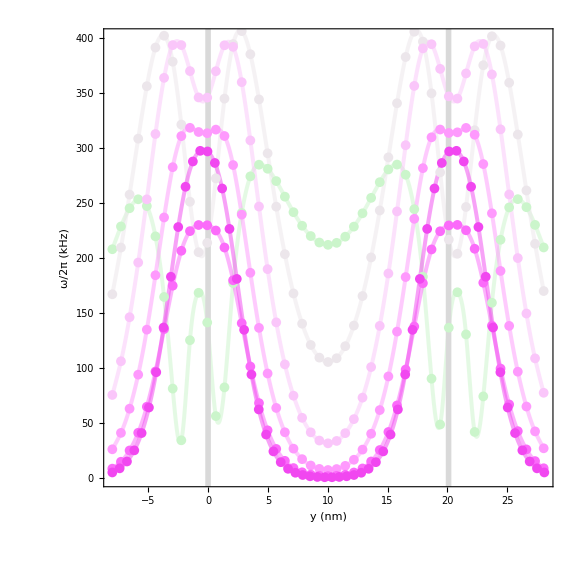

```mathematica
l=((√3)/2*(Num-1))*a;
(*l=3/2*2*Num*a;*)
d=12.5;
F=γe/(2Pi)*μ0/(√a)*√((3μB Ms)/(2l w))*10^-3; (*kHz*)

MANRcup215=Import["C:\\Users\\jeffc\\Documents\\MANR-SCQ_full_strip_omega=2.15.mx"];
MANRcup220=Import["C:\\Users\\jeffc\\Documents\\MANR-SCQ_full_strip_omega=2.2.mx"];
MANRcup225=Import["C:\\Users\\jeffc\\Documents\\MANR-SCQ_full_strip_omega=2.25.mx"];
MANRcup230=Import["C:\\Users\\jeffc\\Documents\\MANR-SCQ_full_strip_omega=2.3.mx"];
MANRcup235=Import["C:\\Users\\jeffc\\Documents\\MANR-SCQ_full_strip_omega=2.35.mx"];
MANRcup240=Import["C:\\Users\\jeffc\\Documents\\MANR-SCQ_full_strip_omega=2.4.mx"];

MANRcup240Scaled=Table[Table[{MANRcup240[[i]][[j]][[1]],2*MANRcup240[[i]][[j]][[2]]},{j,1,Length[MANRcup240[[i]]]}],{i,1,Length[MANRcup240]}];

MANRcup={MANRcup215,MANRcup220,MANRcup225,MANRcup230,MANRcup235,MANRcup240Scaled};
MANRcupCom=Table[Table[{MANRcup[[j]][[1]][[i]][[1]],MANRcup[[j]][[1]][[i]][[2]]+MANRcup[[j]][[2]][[i]][[2]]},{i,1,Length[MANRcup[[j]][[1]]]}],{j,1,Length[MANRcup]}];
MANRcupNames={"MANR-SCQ_Couple_omega=2.15.mx","2.2","2.25","2.3","2.35","2.4"};

pee1=Show[Table[ListPlot[MANRcupCom[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorData["GreenPinkTones",(6+j)/16],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",ImageSize->Large,PlotMarkers->{Automatic,Medium}],{j,1,Length[MANRcupCom]}],PlotRange->All];
pee1smooth=Show[Table[ListPlot[MANRcupCom[[j]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[ColorData["GreenPinkTones",(6+j)/16],Opacity[0.5],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",ImageSize->Large],{j,1,Length[MANRcupCom]}],PlotRange->All];
Show[pee1smooth,pee1,FrameStyle->Thickness[0.01],GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],PlotRange->{All,{0,400}},AspectRatio->1]
```

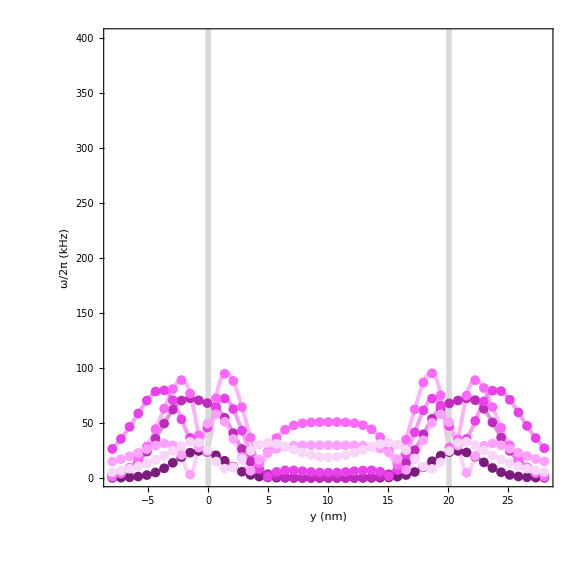

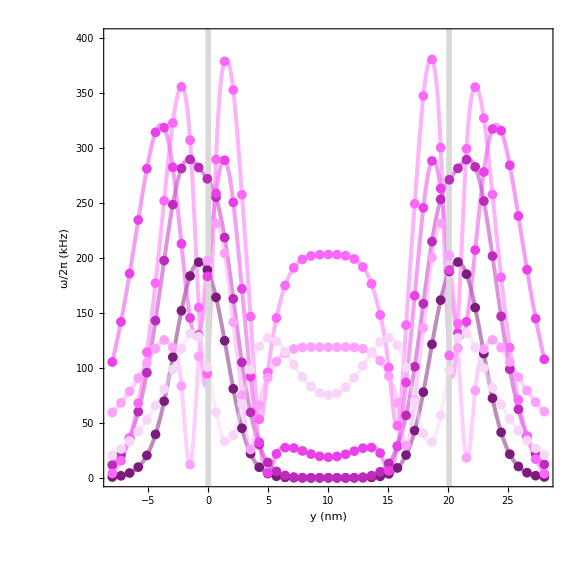

{{{-8.,0.00560663},{-7.27924,0.00562042},{-6.55847,0.0056339},{-5.83771,0.00564706},{-5.11694,0.0056599},{-4.39618,0.00567242},{-3.67542,0.00568461},{-2.95465,0.00569648},{-2.23389,0.00570803},{-1.51312,0.00571924},{-0.79236,0.00573012},{-0.0715961,0.00574067},{0.649168,0.00575087},{1.36993,0.00576074},{2.0907,0.00577027},{2.81146,0.00577946},{3.53222,0.00578829},{4.25299,0.00579677},{4.97375,0.00580485},{5.69452,0.00581246},{6.41528,0.00581932},{7.13604,0.00582453},{7.85681,0.00582531},{8.57757,0.00581291},{9.29834,0.00576014},{10.0191,0.00558347},{10.7399,0.00502974},{11.4606,0.00334456},{12.1814,0.00166959},{12.9022,0.0162292},{13.6229,0.0572285},{14.3437,0.168135},{15.0644,0.452463},{15.7852,1.13039},{16.506,2.59531},{17.2267,5.3641},{17.9475,9.73288},{18.6683,15.1642},{19.389,20.1835},{20.1098,23.4505},{20.8306,24.5067},{21.5513,23.13},{22.2721,19.3314},{22.9929,14.1136},{23.7136,9.04304},{24.4344,5.16921},{25.1551,2.68841},{25.8759,1.29505},{26.5967,0.585868},{27.3174,0.250869},{28.0382,0.101424}},{{-8.,0.0945567},{-7.27924,0.235028},{-6.55847,0.551077},{-5.83771,1.22336},{-5.11694,2.55252},{-4.39618,4.93881},{-3.67542,8.70677},{-2.95465,13.7135},{-2.23389,18.9735},{-1.51312,22.9253},{-0.79236,24.4915},{-0.0715961,23.6071},{0.649168,20.4972},{1.36993,15.5725},{2.0907,10.1141},{2.81146,5.63402},{3.53222,2.75},{4.25299,1.2062},{4.97375,0.485595},{5.69452,0.181453},{6.41528,0.062261},{7.13604,0.018046},{7.85681,0.00230316},{8.57757,0.00312942},{9.29834,0.00495832},{10.0191,0.00556032},{10.7399,0.00575294},{11.4606,0.00581092},{12.1814,0.00582502},{12.9022,0.00582479},{13.6229,0.00581977},{14.3437,0.00581299},{15.0644,0.00580542},{15.7852,0.00579737},{16.506,0.00578892},{17.2267,0.00578011},{17.9475,0.00577095},{18.6683,0.00576145},{19.389,0.00575161},{20.1098,0.00574143},{20.8306,0.00573091},{21.5513,0.00572006},{22.2721,0.00570887},{22.9929,0.00569735},{23.7136,0.00568551},{24.4344,0.00567333},{25.1551,0.00566084},{25.8759,0.00564802},{26.5967,0.00563489},{27.3174,0.00562143},{28.0382,0.00560767}}}

```mathematica
(*Import data*)
MANRcup290=Import["C:\\Users\\jeffc\\Documents\\MANR-SCQ_full_strip_omega=2.9.mx"];
MANRcup295=Import["C:\\Users\\jeffc\\Documents\\MANR-SCQ_full_strip_omega=2.95.mx"];
MANRcup300=Import["C:\\Users\\jeffc\\Documents\\MANR-SCQ_full_strip_omega=3.mx"];
MANRcup305=Import["C:\\Users\\jeffc\\Documents\\MANR-SCQ_full_strip_omega=3.05.mx"];
MANRcup310=Import["C:\\Users\\jeffc\\Documents\\MANR-SCQ_full_strip_omega=3.1.mx"];
MANRcup315=Import["C:\\Users\\jeffc\\Documents\\MANR-SCQ_full_strip_omega=3.15.mx"];

MANRcup2={MANRcup290,MANRcup295,MANRcup300,MANRcup305,MANRcup310,MANRcup315};
(*Go through above list, create a new list that keeps the first element (position) the same and takes the mean of the left and right edge*)
MANRcup3=Table[Table[{MANRcup2[[j]][[1]][[i]][[1]],MANRcup2[[j]][[1]][[i]][[2]]+MANRcup2[[j]][[2]][[i]][[2]]},{i,1,Length[MANRcup2[[j]][[1]]]}],{j,1,Length[MANRcup2]}];

(*Each table scales the y axis by some factor*)
MANRcup290Scaled=Table[Table[{MANRcup290[[i]][[j]][[1]],8*MANRcup290[[i]][[j]][[2]]},{j,1,Length[MANRcup290[[i]]]}],{i,1,Length[MANRcup290]}];
MANRcup295Scaled=Table[Table[{MANRcup295[[i]][[j]][[1]],4*MANRcup295[[i]][[j]][[2]]},{j,1,Length[MANRcup295[[i]]]}],{i,1,Length[MANRcup295]}];
MANRcup300Scaled=Table[Table[{MANRcup300[[i]][[j]][[1]],4*MANRcup300[[i]][[j]][[2]]},{j,1,Length[MANRcup300[[i]]]}],{i,1,Length[MANRcup300]}];
MANRcup305Scaled=Table[Table[{MANRcup305[[i]][[j]][[1]],4*MANRcup305[[i]][[j]][[2]]},{j,1,Length[MANRcup305[[i]]]}],{i,1,Length[MANRcup305]}];
MANRcup310Scaled=Table[Table[{MANRcup310[[i]][[j]][[1]],4*MANRcup310[[i]][[j]][[2]]},{j,1,Length[MANRcup310[[i]]]}],{i,1,Length[MANRcup310]}];
MANRcup315Scaled=Table[Table[{MANRcup315[[i]][[j]][[1]],4*MANRcup315[[i]][[j]][[2]]},{j,1,Length[MANRcup315[[i]]]}],{i,1,Length[MANRcup315]}];

MANRcup2Scaled={MANRcup290Scaled,MANRcup295Scaled,MANRcup300Scaled,MANRcup305Scaled,MANRcup310Scaled,MANRcup315Scaled};
MANRcup3Scaled=Table[Table[{MANRcup2Scaled[[j]][[1]][[i]][[1]],MANRcup2Scaled[[j]][[1]][[i]][[2]]+MANRcup2Scaled[[j]][[2]][[i]][[2]]},{i,1,Length[MANRcup2Scaled[[j]][[1]]]}],{j,1,Length[MANRcup2Scaled]}];

pee2=Show[Table[ListPlot[MANRcup3[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorData["GreenPinkTones",(13-j)/13],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",ImageSize->Large,PlotMarkers->{Automatic,Medium}],{j,1,Length[MANRcup3]}],PlotRange->All];
pee2smooth=Show[Table[ListPlot[MANRcup3[[j]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[ColorData["GreenPinkTones",(13-j)/13],Opacity[0.5],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",ImageSize->Large],{j,1,Length[MANRcup3]}],PlotRange->All];
Show[pee2smooth,pee2,FrameStyle->Thick,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],PlotRange->{All,{0,400}},AspectRatio->1]

pee2Scaled=Show[Table[ListPlot[MANRcup3Scaled[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorData["GreenPinkTones",(13-j)/13],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",ImageSize->Large,PlotMarkers->{Automatic,Medium}],{j,1,Length[MANRcup3Scaled]}],PlotRange->All];
pee2smoothScaled=Show[Table[ListPlot[MANRcup3Scaled[[j]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[ColorData["GreenPinkTones",(13-j)/13],Opacity[0.5],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",ImageSize->Large],{j,1,Length[MANRcup3Scaled]}],PlotRange->All];
Show[pee2smoothScaled,pee2Scaled,FrameStyle->Thick,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],PlotRange->{All,{0,400}},AspectRatio->1]
```

```mathematica
MANRcupNames={"MANR-SCQ_Couple_omega=2.15_combined_indv.svg","MANR-SCQ_Couple_omega=2.2_combined_indv.svg","MANR-SCQ_Couple_omega=2.25_combined_indv.svg","MANR-SCQ_Couple_omega=2.3_combined_indv.svg","MANR-SCQ_Couple_omega=2.35_combined_indv.svg","MANR-SCQ_Couple_omega=2.4_combined_indv_Scaled.svg"};

Do[
Test1=ListPlot[MANRcupCom[[k]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorData["GreenPinkTones",k/15],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}];
Test1smooth=ListPlot[MANRcupCom[[k]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[ColorData["GreenPinkTones",k/15],Opacity[0.5],Thickness[0.007]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific"];

Test1L=ListPlot[MANRcup[[k]][[1]],PlotRange->All,Joined->False,PlotStyle->Directive[Lighter[Lighter[Red]],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}];
Test1smoothL=ListPlot[MANRcup[[k]][[1]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[Lighter[Lighter[Red]],Dashed,Opacity[0.5],Thickness[0.007]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific"];

Test1R=ListPlot[MANRcup[[k]][[2]],PlotRange->All,Joined->False,PlotStyle->Directive[Lighter[Lighter[Blue]],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}];
Test1smoothR=ListPlot[MANRcup[[k]][[2]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[Lighter[Lighter[Blue]],Dashed,Opacity[0.5],Thickness[0.007]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific"];

plottest=Show[Test1smoothL,Test1L,Test1smoothR,Test1R,Test1smooth,Test1,ImageSize->Large,FrameStyle->Thickness[0.01],GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.01]],PlotMarkers->Automatic,PlotRange->{All,{0,475}}];

Export[MANRcupNames[[k]],plottest]
,{k,1,Length[MANRcupCom]}];
```

```mathematica
LineLegend[Table[ColorData["GreenPinkTones",k/15],{k,1,15}],Automatic,LegendMarkers->{"●",15},LegendMarkerSize->{30,15}]
```

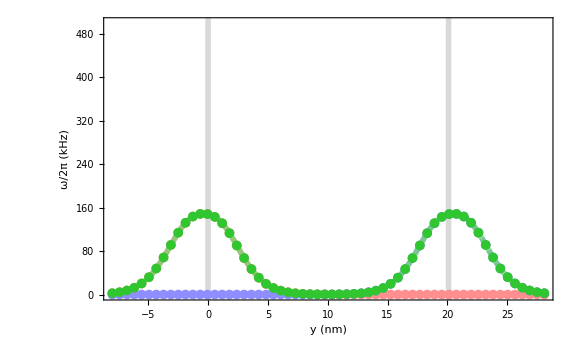

```mathematica
Test1=ListPlot[MANRcupCom[[6]],PlotRange->All,Joined->False,PlotStyle->Directive[Blend[{Darker[Green],Lighter[Lighter[Green]]},4/12],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->28}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}];
Test1smooth=ListPlot[MANRcupCom[[6]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[Blend[{Darker[Green],Lighter[Lighter[Green]]},4/12],Opacity[0.5],Thickness[0.007]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->28}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"];

Test1L=ListPlot[MANRcup[[6]][[1]],PlotRange->All,Joined->False,PlotStyle->Directive[Lighter[Lighter[Red]],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->28}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}];
Test1smoothL=ListPlot[MANRcup[[6]][[1]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[Lighter[Lighter[Red]],Dashed,Opacity[0.5],Thickness[0.007]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->28}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"];

Test1R=ListPlot[MANRcup[[6]][[2]],PlotRange->All,Joined->False,PlotStyle->Directive[Lighter[Lighter[Blue]],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->28}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}];
Test1smoothR=ListPlot[MANRcup[[6]][[2]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[Lighter[Lighter[Blue]],Dashed,Opacity[0.5],Thickness[0.007]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->28}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"];

plottest=Show[Test1smoothL,Test1L,Test1smoothR,Test1R,Test1smooth,Test1,ImageSize->Large,FrameStyle->Thick,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],PlotMarkers->Automatic,PlotRange->{All,{0,500}}]
```

```mathematica
MANRcupNames={"MANR-SCQ_Couple_omega=2.9_combined_indv_Scaled.svg","MANR-SCQ_Couple_omega=2.95_combined_indv_Scaled.svg","MANR-SCQ_Couple_omega=3_combined_indv_Scaled.svg","MANR-SCQ_Couple_omega=3.05_combined_indv_Scaled.svg","MANR-SCQ_Couple_omega=3.1_combined_indv_Scaled.svg","MANR-SCQ_Couple_omega=3.15_combined_indv_Scaled.svg"};

ColorzzzL={Lighter[Lighter[Blue]],Lighter[Lighter[Blue]],Lighter[Lighter[Blue]],Lighter[Lighter[Blue]],Lighter[Lighter[Red]],Lighter[Lighter[Red]]};
ColorzzzR={Lighter[Lighter[Red]],Lighter[Lighter[Red]],Lighter[Lighter[Red]],Lighter[Lighter[Red]],Lighter[Lighter[Blue]],Lighter[Lighter[Blue]]};

Do[
Test1=ListPlot[MANRcup3Scaled[[k]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorData["GreenPinkTones",(9+k)/15],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}];
Test1smooth=ListPlot[MANRcup3Scaled[[k]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[ColorData["GreenPinkTones",(9+k)/15],Opacity[0.5],Thickness[0.007]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"];

Test1L=ListPlot[MANRcup2Scaled[[k]][[1]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorzzzL[[k]],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}];
Test1smoothL=ListPlot[MANRcup2Scaled[[k]][[1]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[ColorzzzL[[k]],Dashed,Opacity[0.5],Thickness[0.007]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"];

Test1R=ListPlot[MANRcup2Scaled[[k]][[2]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorzzzR[[k]],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}];
Test1smoothR=ListPlot[MANRcup2Scaled[[k]][[2]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[ColorzzzR[[k]],Dashed,Opacity[0.5],Thickness[0.007]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"];

plottest=Show[Test1smoothL,Test1L,Test1smoothR,Test1R,Test1smooth,Test1,ImageSize->Large,FrameStyle->Thickness[0.01],GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.01]],PlotMarkers->Automatic,PlotRange->{All,{0,475}}];

Export[MANRcupNames[[k]],plottest]
,{k,1,Length[MANRcup3]}];
```

```mathematica
MANRcupNames={"MANR-SCQ_Couple_omega=2.525_combined_indv_Scaled.svg","MANR-SCQ_Couple_omega=2.65_combined_indv_Scaled.svg","MANR-SCQ_Couple_omega=2.775_combined_indv_Scaled.svg"};

MANRcup2525=Import["C:\\Users\\jeffc\\Documents\\MANR-SCQ_full_strip_omega=2.525.mx"];
MANRcup265=Import["C:\\Users\\jeffc\\Documents\\MANR-SCQ_full_strip_omega=2.65.mx"];
MANRcup2775=Import["C:\\Users\\jeffc\\Documents\\MANR-SCQ_full_strip_omega=2.775.mx"];

MANRcupMid={MANRcup2525,MANRcup265,MANRcup2775};
MANRcupMidCom=Table[Table[{MANRcupMid[[j]][[1]][[i]][[1]],MANRcupMid[[j]][[1]][[i]][[2]]+MANRcupMid[[j]][[2]][[i]][[2]]},{i,1,Length[MANRcupMid[[j]][[1]]]}],{j,1,Length[MANRcupMid]}];

MANRcup2525Scaled=Table[Table[{MANRcup2525[[i]][[j]][[1]],8*MANRcup2525[[i]][[j]][[2]]},{j,1,Length[MANRcup2525[[i]]]}],{i,1,Length[MANRcup2525]}];
MANRcup265Scaled=Table[Table[{MANRcup265[[i]][[j]][[1]],50*MANRcup265[[i]][[j]][[2]]},{j,1,Length[MANRcup265[[i]]]}],{i,1,Length[MANRcup265]}];
MANRcup2775Scaled=Table[Table[{MANRcup2775[[i]][[j]][[1]],50*MANRcup2775[[i]][[j]][[2]]},{j,1,Length[MANRcup2775[[i]]]}],{i,1,Length[MANRcup2775]}];

MANRcupMidScaled={MANRcup2525Scaled,MANRcup265Scaled,MANRcup2775Scaled};
MANRcupMidComScaled=Table[Table[{MANRcupMidScaled[[j]][[1]][[i]][[1]],MANRcupMidScaled[[j]][[1]][[i]][[2]]+MANRcupMidScaled[[j]][[2]][[i]][[2]]},{i,1,Length[MANRcupMidScaled[[j]][[1]]]}],{j,1,Length[MANRcupMidScaled]}];

ColorzzzL={Lighter[Lighter[Blue]],Lighter[Lighter[Blue]],Lighter[Lighter[Red]]};
ColorzzzR={Lighter[Lighter[Red]],Lighter[Lighter[Red]],Lighter[Lighter[Blue]]};

Do[
Test1=ListPlot[MANRcupMidComScaled[[k]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorData["GreenPinkTones",(6+k)/15],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}];
Test1smooth=ListPlot[MANRcupMidComScaled[[k]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[ColorData["GreenPinkTones",(6+k)/15],Opacity[0.5],Thickness[0.007]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"];

Test1L=ListPlot[MANRcupMidScaled[[k]][[1]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorzzzL[[k]],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}];
Test1smoothL=ListPlot[MANRcupMidScaled[[k]][[1]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[ColorzzzL[[k]],Dashed,Opacity[0.5],Thickness[0.007]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"];

Test1R=ListPlot[MANRcupMidScaled[[k]][[2]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorzzzR[[k]],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}];
Test1smoothR=ListPlot[MANRcupMidScaled[[k]][[2]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[ColorzzzR[[k]],Dashed,Opacity[0.5],Thickness[0.007]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"];

plottest=Show[Test1smoothL,Test1L,Test1smoothR,Test1R,Test1smooth,Test1,ImageSize->Large,FrameStyle->Thickness[0.01],GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.01]],PlotMarkers->Automatic,PlotRange->{All,{0,475}}];

Export[MANRcupNames[[k]],plottest]
,{k,1,Length[MANRcupMidScaled]}];
```

### Edge Couple vs. d

```mathematica
Num=59;

mom=MeanMom[3.15,0.01][[1]][[2]];
numba=MeanMom[3.15,0.01][[1]][[1]];
l=((√3)/2*Num-1)*a;
(*l=3/2*2*Num*a;*)
F=γe/(2Pi)*μ0/(√a)*√((3μB Ms)/(2l w))*10^-3; (*kHz*)
Gmax=Table[{r,F*MANRCouplingDiscreteTest[J,J2,DM,s,0,h,ϕ,mom,Num,numba,0,0,r,-3*300,3*300]},{r,0.1,25.1,0.5}];
```

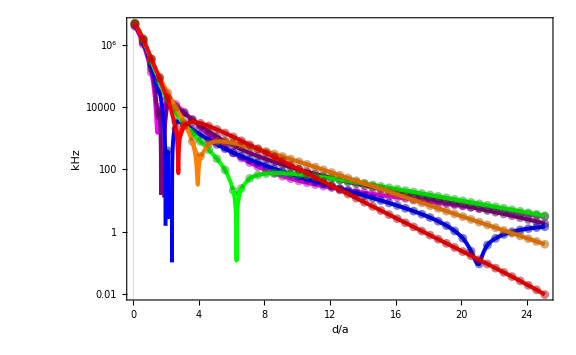

```mathematica
Export["MANR_edge_couple_omega=3.15.mx",Gmax];
(*edge1smZZ=ListLogPlot[Gmax,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[Red,Thickness[.01],Opacity[0.5]],PlotTheme->"Scientific",Joined->True,PlotRange->All,ImageSize->Large];*)

TestEmptyList={};
Do[
AppendTo[TestEmptyList,Gmax[[j]][[2]]]
,{j,1,Length[Gmax]}]

v=ListInterpolation[TestEmptyList,{0.1,25.1}];
edge6sm=LogPlot[v[x],{x,0.1,25.1},LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","kHz"},PlotStyle->Directive[Magenta,Thickness[0.005]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,Exclusions->Range[3.6,4.1]];

edge6=ListLogPlot[Gmax,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[Darker[Magenta],Thickness[.01],Opacity[0.5]],PlotTheme->"Scientific",Joined->False,PlotRange->All,ImageSize->Large];

Show[edge6sm,edge6,edge5sm,edge5,edge4sm,edge4,edge3sm,edge3,edge3smZ,edge2sm,edge2,edge2smZ,edge1sm,edge1,edge1smZ]
```

```mathematica
F*MANRCouplingDiscreteTest[J,J2,DM,s,0,h,ϕ,mom,Num,numba,0,0,2.11,-3*500,3*500]
```

192.669

```mathematica
MeanMom[3.1,0.01]
```

{{62,0.0471239,3.10025},{62,-0.0471239,3.10025}}

```mathematica
(*PointLegend[{Darker[Red],Darker[Orange],Darker[Green],Darker[Blue],Darker[Purple],Darker[Magenta]},{MeanMom[2.15,0.01][[1]][[2]],MeanMom[2.2,0.01][[1]][[2]],MeanMom[2.25,0.01][[1]][[2]],MeanMom[2.3,0.01][[1]][[2]],MeanMom[2.35,0.01][[1]][[2]],MeanMom[2.5,0.01][[1]][[2]]}]*)
MeanMom[2.6,0.01][[1]][[2]]
```

0.76969

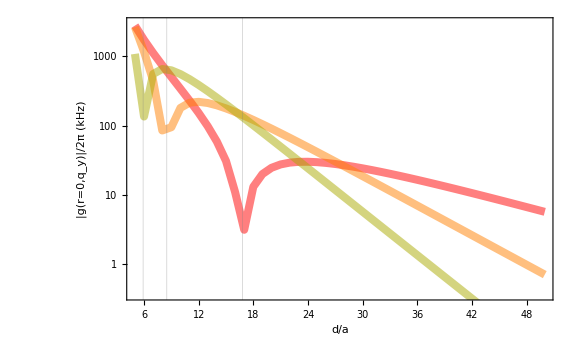

```mathematica
Show[p1,p2,p3,PlotRange->{{5,50},{-1,8}},GridLines->{{5.9,8.5,16.8},{}}]
```

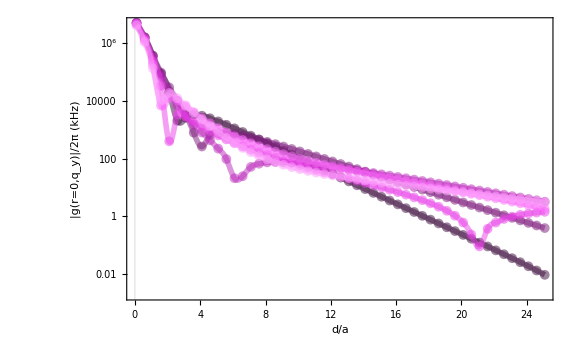

```mathematica
MANRedge315=Import["MANR_edge_couple_omega=3.15.mx"];
MANRedge31=Import["MANR_edge_couple_omega=3.1.mx"];
MANRedge305=Import["MANR_edge_couple_omega=3.05.mx"];
MANRedge3=Import["MANR_edge_couple_omega=3.mx"];
MANRedge295=Import["MANR_edge_couple_omega=2.95.mx"];
MANRedge29=Import["MANR_edge_couple_omega=2.9.mx"];

MANRedge={MANRedge29,MANRedge295,MANRedge3,MANRedge305,MANRedge31,MANRedge315};

(*MZNRedge315=Import["MZNR-SCQ_edge_vs_d_omega=3.15.mx"];
MZNRedge31=Import["MZNR-SCQ_edge_vs_d_omega=3.1.mx"];
MZNRedge305=Import["MZNR-SCQ_edge_vs_d_omega=3.05.mx"];
MZNRedge3=Import["MZNR-SCQ_edge_vs_d_omega=3.mx"];
MZNRedge295=Import["MZNR-SCQ_edge_vs_d_omega=2.95.mx"];
MZNRedge29=Import["MZNR-SCQ_edge_vs_d_omega=2.9.mx"];*)

edge1=ListLogPlot[MANRedge29,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[ColorData["GreenPinkTones",1],Thickness[.01],Opacity[0.5]],PlotTheme->"Scientific",Joined->False,PlotRange->All,ImageSize->Large,PlotMarkers->{Automatic,Medium}];
edge1smooth=ListLogPlot[MANRedge29,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[ColorData["GreenPinkTones",1],Thickness[0.007],Opacity[0.5]],PlotTheme->"Scientific",Joined->True,InterpolationOrder->10,PlotRange->All,ImageSize->Large];
edge2=ListLogPlot[MANRedge295,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[ColorData["GreenPinkTones",12/13],Thickness[.01],Opacity[0.5]],PlotTheme->"Scientific",Joined->False,PlotRange->All,ImageSize->Large,PlotMarkers->{Automatic,Medium}];
edge2smooth=ListLogPlot[MANRedge295,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[ColorData["GreenPinkTones",12/13],Thickness[0.007],Opacity[0.5]],PlotTheme->"Scientific",Joined->True,InterpolationOrder->3,PlotRange->All,ImageSize->Large];
edge3=ListLogPlot[MANRedge3,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[ColorData["GreenPinkTones",11/13],Thickness[.01],Opacity[0.5]],PlotTheme->"Scientific",Joined->False,PlotRange->All,ImageSize->Large,PlotMarkers->{Automatic,Medium}];
edge3smooth=ListLogPlot[MANRedge3,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[ColorData["GreenPinkTones",11/13],Thickness[0.007],Opacity[0.5]],PlotTheme->"Scientific",Joined->True,InterpolationOrder->3,PlotRange->All,ImageSize->Large];
edge4=ListLogPlot[MANRedge305,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[ColorData["GreenPinkTones",10/13],Thickness[.01],Opacity[0.5]],PlotTheme->"Scientific",Joined->False,PlotRange->All,ImageSize->Large,PlotMarkers->{Automatic,Medium}];
edge4smooth=ListLogPlot[MANRedge305,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[ColorData["GreenPinkTones",10/13],Thickness[0.007],Opacity[0.5]],PlotTheme->"Scientific",Joined->True,InterpolationOrder->3,PlotRange->All,ImageSize->Large];
edge5=ListLogPlot[MANRedge31,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[ColorData["GreenPinkTones",9/13],Thickness[.01],Opacity[0.5]],PlotTheme->"Scientific",Joined->False,PlotRange->All,ImageSize->Large,PlotMarkers->{Automatic,Medium}];
edge5smooth=ListLogPlot[MANRedge31,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[ColorData["GreenPinkTones",9/13],Thickness[0.007],Opacity[0.5]],PlotTheme->"Scientific",Joined->True,InterpolationOrder->3,PlotRange->All,ImageSize->Large];
edge6=ListLogPlot[MANRedge315,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[ColorData["GreenPinkTones",8/13],Thickness[0.007],Opacity[0.5]],PlotTheme->"Scientific",Joined->False,PlotRange->All,ImageSize->Large,PlotMarkers->{Automatic,Medium}];
edge6smooth=ListLogPlot[MANRedge315,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[ColorData["GreenPinkTones",8/13],Thickness[0.007],Opacity[0.5]],PlotTheme->"Scientific",Joined->True,InterpolationOrder->3,PlotRange->All,ImageSize->Large];

(*Zedge1=ListLogPlot[MZNRedge29,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[Red,Thickness[.01],Opacity[0.5]],PlotTheme->"Scientific",Joined->False,PlotMarkers->Graphics[{Rectangle[]},ImageSize->8],PlotRange->All,ImageSize->Large];
Zedge1smooth=ListLogPlot[MZNRedge29,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[Lighter[Red],Thick,Opacity[0.5]],PlotTheme->"Scientific",Joined->True,InterpolationOrder->10,PlotRange->All,ImageSize->Large];
Zedge2=ListLogPlot[MZNRedge295,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[Orange,Thickness[.01],Opacity[0.5]],PlotTheme->"Scientific",Joined->False,PlotMarkers->Graphics[{Rectangle[]},ImageSize->8],PlotRange->All,ImageSize->Large];
Zedge2smooth=ListLogPlot[MZNRedge295,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[Lighter[Orange],Thick,Opacity[0.5]],PlotTheme->"Scientific",Joined->True,InterpolationOrder->3,PlotRange->All,ImageSize->Large];
Zedge3=ListLogPlot[MZNRedge3,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[Green,Thickness[.01],Opacity[0.5]],PlotTheme->"Scientific",Joined->False,PlotMarkers->Graphics[{Rectangle[]},ImageSize->8],PlotRange->All,ImageSize->Large];
Zedge3smooth=ListLogPlot[MZNRedge3,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[Lighter[Green],Thick,Opacity[0.5]],PlotTheme->"Scientific",Joined->True,InterpolationOrder->3,PlotRange->All,ImageSize->Large];
Zedge4=ListLogPlot[MZNRedge305,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[Blue,Thickness[.01],Opacity[0.5]],PlotTheme->"Scientific",Joined->False,PlotMarkers->Graphics[{Rectangle[]},ImageSize->8],PlotRange->All,ImageSize->Large];
Zedge4smooth=ListLogPlot[MANRedge305,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[Lighter[Blue],Thick,Opacity[0.5]],PlotTheme->"Scientific",Joined->True,InterpolationOrder->3,PlotRange->All,ImageSize->Large];
Zedge5=ListLogPlot[MZNRedge31,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[Purple,Thickness[.01],Opacity[0.5]],PlotTheme->"Scientific",Joined->False,PlotMarkers->Graphics[{Rectangle[]},ImageSize->8],PlotRange->All,ImageSize->Large];
Zedge5smooth=ListLogPlot[MZNRedge31,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[Lighter[Purple],Thick,Opacity[0.5]],PlotTheme->"Scientific",Joined->True,InterpolationOrder->3,PlotRange->All,ImageSize->Large];
Zedge6=ListLogPlot[MZNRedge315,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[Magenta,Thickness[.01],Opacity[0.5]],PlotTheme->"Scientific",Joined->False,PlotMarkers->Graphics[{Rectangle[]},ImageSize->8],PlotRange->All,ImageSize->Large];
Zedge6smooth=ListLogPlot[MZNRedge315,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotStyle->Directive[Lighter[Purple],Thick,Opacity[0.5]],PlotTheme->"Scientific",Joined->True,InterpolationOrder->3,PlotRange->All,ImageSize->Large];*)

Show[(*Zedge1,Zedge1smooth,Zedge2,Zedge2smooth,Zedge3,Zedge3smooth,Zedge4,Zedge4smooth,Zedge5,Zedge5smooth,Zedge6,Zedge6smooth,*)edge1,edge1smooth,edge2,edge2smooth,edge3,edge3smooth,edge4,edge4smooth,edge5,edge5smooth,edge6,edge6smooth]
(*Show[edge1,edge2,edge3,edge4,edge5,edge6]
Show[edge1smooth,edge2smooth,edge3smooth,edge4smooth,edge5smooth,edge6smooth]
*)
```

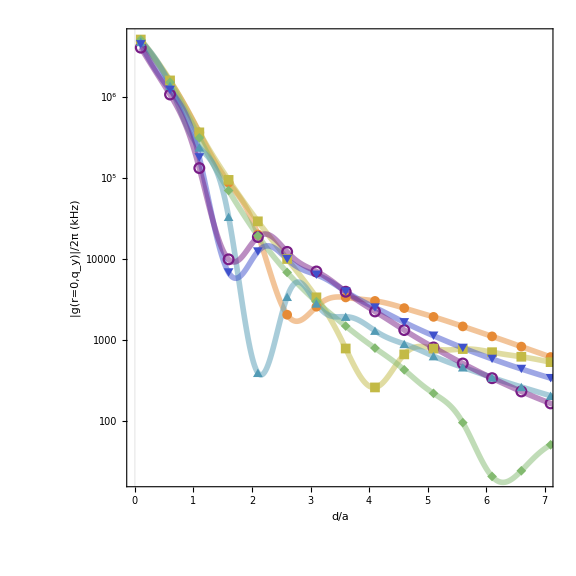

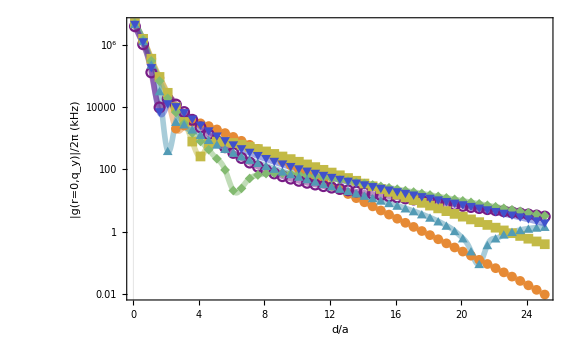

{Directive[RGBColor[0.4426345, 0.09391447500000001, 0.4414659375],Thickness[Large]],Directive[RGBColor[0.654277875, 0.14034155, 0.654215875],Thickness[Large]],Directive[RGBColor[0.8381316249999999, 0.1935443125, 0.83727525],Thickness[Large]],Directive[RGBColor[0.94342975, 0.2775385, 0.9399735],Thickness[Large]],Directive[RGBColor[0.9856093749999999, 0.418897, 0.9809864375],Thickness[Large]],Directive[RGBColor[0.995495625, 0.600393875, 0.991828625],Thickness[Large]]}

```mathematica
edge1prime=ListLogPlot[MANRedge,PlotStyle->Table[Directive[ColorData["Rainbow",(6-j)/6]],{j,1,6}],Joined->False,PlotMarkers->{Automatic, Medium},LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotTheme->"Scientific",PlotRange->All,ImageSize->Large];
edge1primesmooth=ListLogPlot[MANRedge,PlotStyle->Table[Directive[ColorData["Rainbow",(6-j)/6],Thickness[0.007],Opacity[0.5]],{j,1,6}],Joined->True,InterpolationOrder->5,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","|g(r=0,q_y)|/2π (kHz)"},PlotTheme->"Scientific",PlotRange->All,ImageSize->Large];
Show[edge1primesmooth,edge1prime,PlotRange->{{0,7},{3,15.5}},ImageSize->Large,AspectRatio->1,FrameStyle->Thick,GridLinesStyle->Thick]
Show[edge1primesmooth,edge1prime,PlotRange->All,ImageSize->Large,FrameStyle->Thick,GridLinesStyle->Thick]
```

### Coupling vs. ω

```mathematica
Num=59;

l=((√3)/2*Num-1)*a;
(*l=3/2*2*Num*a;*)
d=12.5;
F=γe/(2Pi)*μ0/(√a)*√((3μB Ms)/(2l w))*10^-3; (*kHz*)
Gmax=Table[{ω,F*MANRCouplingDiscreteTest[J,J2,DM,s,0,h,ϕ,MeanMom[ω,0.01][[1]][[2]],Num,MeanMom[ω,0.01][[1]][[1]],5,0,d,-3*400,3*400]},{ω,2.15,2.4,0.01}];
```

```mathematica
p5=ListLogPlot[Gmax,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"d/a","|g_Max(k)|/2π (kHz)"},PlotStyle->Directive[Red,Thickness[.01]],PlotTheme->"Scientific",Joined->False,PlotRange->All,ImageSize->Large];

TestEmptyList={};
Do[
AppendTo[TestEmptyList,Gmax[[j]][[2]]]
,{j,1,Length[Gmax]}];


v=ListInterpolation[TestEmptyList,{2.15,2.4}];
p51=LogPlot[Abs[v[x]],{x,2.15,2.4},LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"ω/2π (THz)","|g(k)|/2π (kHz)"},PlotStyle->Directive[Red,Thickness[0.005],Opacity[0.75]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large];
```

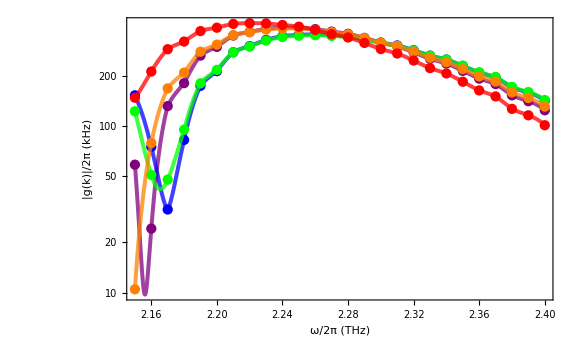

```mathematica
Show[p11,p1,p21,p2,p31,p3,p41,p4,p51,p5]
```

```mathematica
F*MANRCouplingDiscreteTest[J,J2,DM,s,5,h,ϕ,(-1)^(MeanMom[3.06,0.01][[1]][[1]])MeanMom[3.06,0.01][[1]][[2]],Num,MeanMom[3.06,0.01][[1]][[1]],0,0,d,-3*500,3*500]
```

1668.16

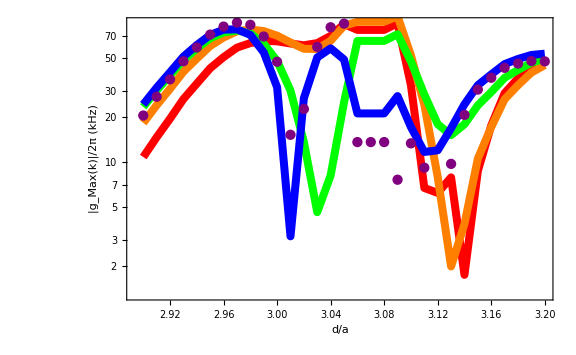

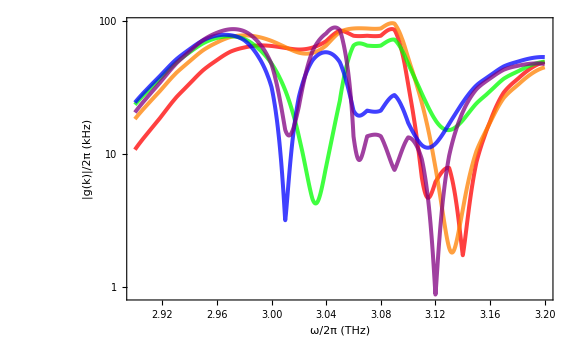

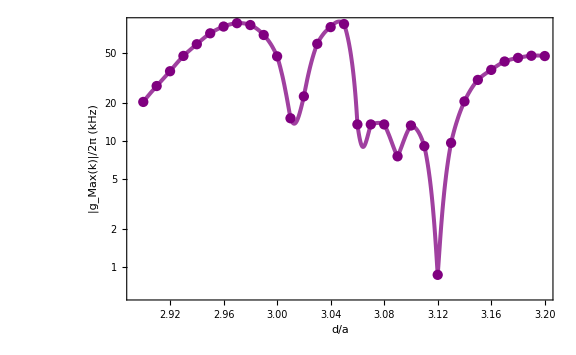

```mathematica
Show[p1,p2,p3,p4,p5]
Show[p11,p21,p31,p41,p51]
Show[p5,p51]
```

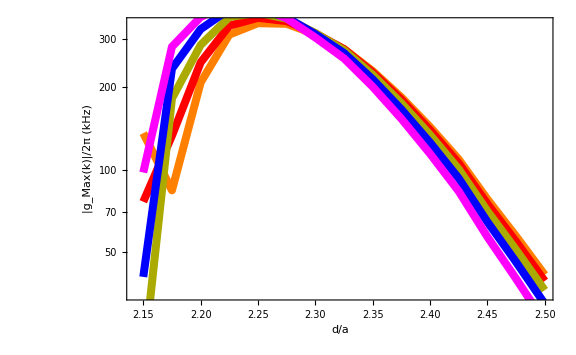

```mathematica
Show[p2,p3,p4,p5,p6]
```

```mathematica
F*MANRCouplingDiscreteTest[J,J2,DM,s,0,h,ϕ,-MeanMom[2.9,0.01][[1]][[2]],Num,MeanMom[2.9,0.01][[1]][[1]],0,0,d,-3*300,3*300]
```

23.3993

```mathematica
MeanMom[2.9,0.01]
MeanMom[3.1,0.01]
```

{{61,0.586431,2.90016},{61,-0.586431,2.90016}}

{{62,0.0471239,3.10025},{62,-0.0471239,3.10025}}

### Stray Field Vs. d/a

```mathematica
Num=59;

mom=MeanMom[2.9,0.01][[2]][[2]];
numba=MeanMom[2.9,0.01][[2]][[1]];
l=((√3)/2*Num-1)*a;
(*l=3/2*2*Num*a;*)
F=γe/(2Pi)*μ0/(√a)*√((3μB Ms)/(2l w))*10^-3; (*kHz*)
stray=Table[{r,MANRStrayField[J,J2,DM,s,0,h,ϕ,mom,Num,numba,0,0,r,-3*300,3*300,2]},{r,2,25,0.5}];

Export["MANR_hy_omega=2.9.mx",stray];
```

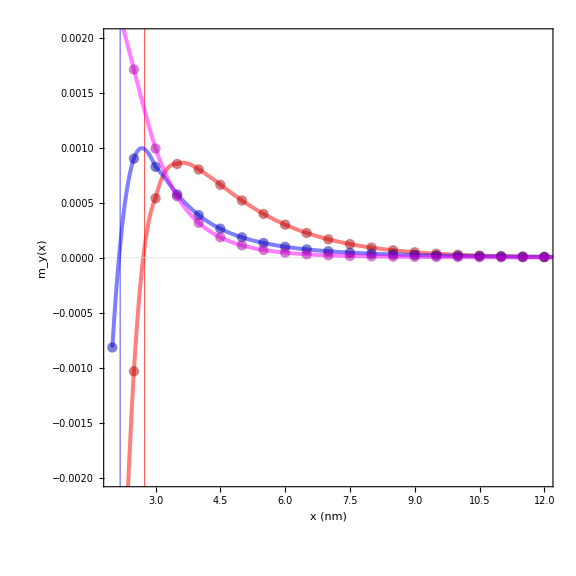

```mathematica
hy1=ListPlot[stray,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"d/a","h (a.u.)"},PlotStyle->Directive[Red,Thickness[.01],Opacity[0.5]],PlotTheme->"Scientific",Joined->False,PlotRange->All,ImageSize->Large,GridLines->{{},{0}},GridLinesStyle->Directive[Thick],FrameStyle->Directive[Thick]];

TestEmptyListy={};
Do[
AppendTo[TestEmptyListy,stray[[j]][[2]]]
,{j,1,Length[stray]}]

strayfield=ListInterpolation[TestEmptyListy,{2,25}];
hy11=Plot[strayfield[x],{x,2,25},LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->28}],FrameLabel->{"x (nm)","m_y(x)"},PlotStyle->Directive[Lighter[Red],Thickness[0.005],Opacity[0.5]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,FrameStyle->Directive[Thick],GridLinesStyle->Directive[Thickness[0.005]]];

(*Show[hx31,hx3,hx11,hx1,hx21,hx2,AspectRatio->1/GoldenRatio,PlotRange->{All,{-0.002,0.002}},GridLines->{{{2.18,Blue},{2.75,Red},{21,Blue}},{0}}]*)

Show[hx11,hx1,hx21,hx2,hx31,hx3,AspectRatio->1,PlotRange->{{2,12},{-0.002,0.002}},GridLines->{{{2.18,Blue},{2.75,Red},{21,Blue}},{0}}]
```

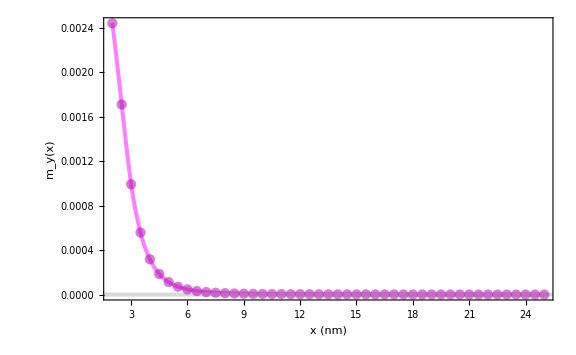

```mathematica
Show[hx31,hx3]
```

```mathematica
MANRStrayField[J,J2,DM,s,0,h,ϕ,mom,Num,numba,0,0,2.9,-3*300,3*300,2]
```

0.000836259+0. ⅈ

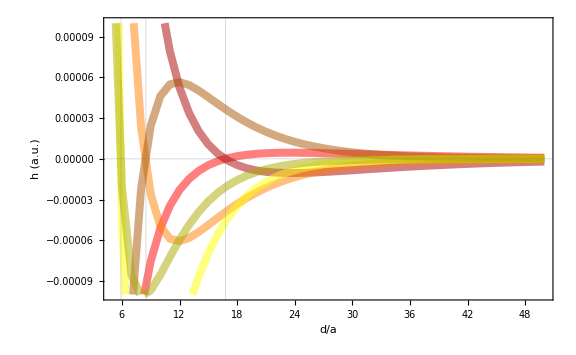

```mathematica
Show[h1,h2,h3,h4,h5,h6,GridLines->{{5.9,8.5,16.8},{0}}]
```

```mathematica
F
γe/(2Pi)*μ0/(√a)*√((3μB Ms)/(2*(3/2*40-1)*a*w))*10^-3
```

5.29575×10^6

4.87978×10^6

### Stray Field vs. Strip Width

```mathematica
Num=59;

l=((√3)/2*Num-1)*a;
(*l=3/2*2*Num*a;*)
F=γe/(2Pi)*μ0/(√a)*√((3μB Ms)/(2l w))*10^-3; (*kHz*)

ω=2.15;
error=0.01;
NSteps=50;

MagFieldList={};

Do[
numba=MeanMom[ω,error][[j]][[1]];
mom=MeanMom[ω,error][[j]][[2]];
Do[
x=-20+j*N[(l/a+40)/NSteps];
y=0;
gx=MANRStrayField[J,J2,DM,s,0,h,ϕ,mom,Num,numba,x,y,12.5,-3*200,3*200,1];
gm[x]={0.4*x,gx};
,{j,0,NSteps}];

AppendTo[MagFieldList,Table[gm[x],{x,-20,l/a+20,N[(l/a+40)/NSteps]}]];

,{j,1,Length[MeanMom[ω,error]]}];
```

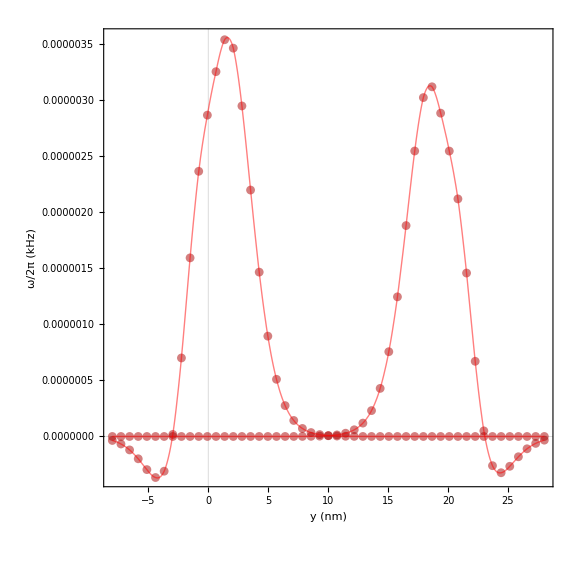

```mathematica
mag1x1=Show[Table[ListPlot[MagFieldList[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[Darker[Red],Thick,Opacity[0.5]],
LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"],{j,1,Length[MagFieldList]}],ImageSize->Large,PlotRange->All,AspectRatio->1];

TestEmptyList={};
Do[
Do[
AppendTo[TestEmptyList,MagFieldList[[i]][[j]][[2]]]
,{j,1,Length[MagFieldList[[i]]]}];
,{i,1,Length[MagFieldList]}];.

Do[

v=ListInterpolation[TestEmptyList[[Length[MagFieldList[[j]]]*(j-1)+1;;Length[MagFieldList[[j]]]*j]],{-8,N[l/a+20]*0.4}];
plot[j]=Plot[v[x],{x,-8,N[l/a+20]*0.4},LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"x (nm)","h (a.u.)"},PlotStyle->Directive[Red,Thick,Opacity[0.5]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,PlotLegends->Automatic]
,{j,1,Length[MagFieldList]}];

mag1x=Show[Table[plot[j],{j,1,Length[MagFieldList]}],ImageSize->Large,PlotRange->Full,GridLines->{{0,N[l/a]*0.4},{}},AspectRatio->1];

Show[mag1x1,mag1x]
```

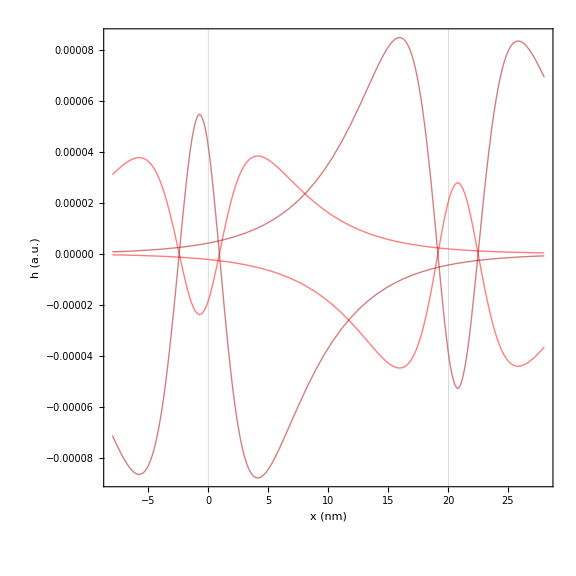

```mathematica
Show[mag1x,mag1y]
```

### How does Coupling Change with Easy-axis Anisotropy?

```mathematica
(*The following function is going to be a little redundant, since it isn't much different than WaveAlgo, but it is my hope
that it will be more efficient.*)

Naux=2000;
Num=59;

(*The following are essentially the same ass FindIndices and MeanMom defined above but with minor alterations to try to increase efficiancy.*)

FindIndices2[Naux_,Num_,lb_,ub_,J_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_]:=
Module[{EmptyList,omegas,H,A,sortorder},

EmptyList={};

Do[
ξ=-Pi/3+j* N[(2 Pi/3)/Naux];

H=MANRMatrix2N[J,J2,DM,s,κ,Δκ,h,ϕ,ξ,Num];

A=Eigensystem[H];

sortorder=Ordering[A[[1]]];

f[ξ]=Table[{ξ ,(A[[1]][[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}];

,{j,0,Naux}];

omegas=Table[Table[f[ξ][[j]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[Naux/2]],{j,1,Length[Table[f[ξ],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[Naux/2]]]}];
(*Note that omegas is the table of frequencies for near-zero momentum. This will suffice for finding the band indices. *)


Do[
If[lb<omegas[[j]]<ub,AppendTo[EmptyList,j]]
,{j,1,Length[omegas]}];

EmptyList
]

MeanMom2[ω_,err_,Naux_,Num_,lb_,ub_,J_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_]:=
Module[{BandIndices,EmptyList,Mom,MomList,EmptyList2},
BandIndices=FindIndices2[Naux,Num,lb,ub,J,J2,DM,s,κ,Δκ,h,ϕ];

EmptyList={};

Do[
Do[
If[ω-err<Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]]<ω+err, AppendTo[EmptyList,{BandIndices[[i]],Table[f[ξ][[BandIndices[[i]]]][[1]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]],Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]]}]]
,{j,1,Length[Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}]]}]
,{i,1,Length[BandIndices]}];

Mom=Sort[EmptyList,Abs[#1[[1]]]<Abs[#2[[1]]]&];

MomList=Split[Mom,Abs[#1[[2]]-#2[[2]]]<err&&#1[[1]]==#2[[1]]&];
EmptyList2={};

For[i=1,i<Length[MomList]+1,i++,AppendTo[EmptyList2,Mean[MomList[[i]]]]];

EmptyList2
]

KappaMom={};

Module[{k,ka,EdgeCouple,mean,numba,κ,Δκ,KappaLine},

κ=0.3;

Do[

Δκ=0+0.03*m;

mean=MeanMom2[3.1+κ/(2Pi ℏ),1/4000,Naux,Num,2.4,3.2,J,J2,DM,s,κ,Δκ,h,ϕ];
k=mean[[1]][[2]];
numba=mean[[1]][[1]];

AppendTo[KappaMom,{Δκ,Around[k,1/4000]}];

,{m,0,10}];

];
```

```mathematica
EdgeCoupleList={};

Module[{ka,EdgeCouple},
Do[

Δκ=0+0.03*m;

ka=KappaMom[[m+1]][[2]][[1]];

EdgeCouple = F*MANRCouplingDiscrete[J,J2,DM,s,κ,Δκ,h,ϕ,ka,Num,numba,0,0,d,-3*300,3*300];

AppendTo[EdgeCoupleList,{Δκ,EdgeCouple}];

,{m,0,10}];
];
```

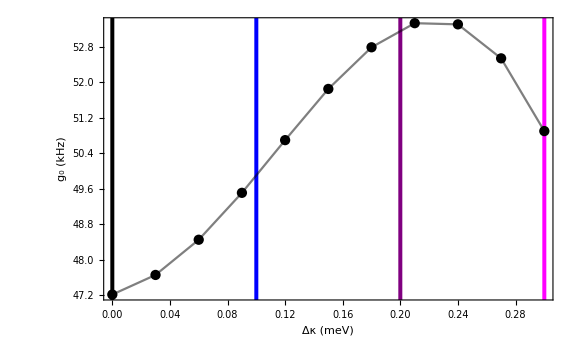

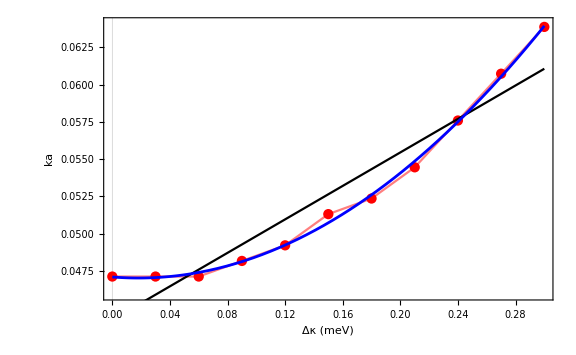

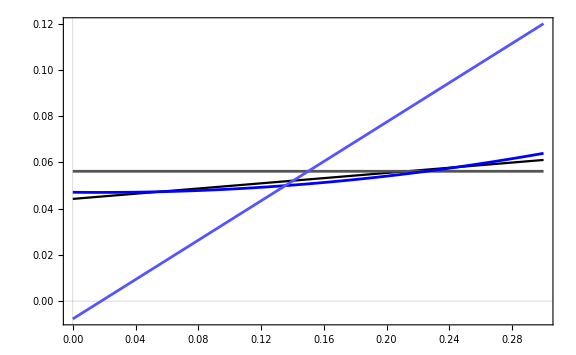

{-0.0470946,-0.0470551,-0.0473987,-0.0481257,-0.0492359,-0.0507293,-0.0526059,-0.0548658,-0.057509,-0.0605353,-0.063945}

```mathematica
thisplot2=ListPlot[EdgeCoupleList,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"Δκ (meV)","g_0 (kHz)"},PlotStyle->Directive[Black],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,AspectRatio->1/GoldenRatio];
thisplotj2=ListPlot[EdgeCoupleList,Joined->True,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω (THz)"},PlotStyle->Directive[Black,Dashed,Opacity[0.5]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,AspectRatio->1];
thisotherplot=ListPlot[KappaMom,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"Δκ (meV)","ka"},PlotStyle->Directive[Red],PlotTheme->"Scientific",ImageSize->Large,AspectRatio->1];
thisotherplotj=ListPlot[KappaMom,Joined->True,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω (THz)"},PlotStyle->Directive[Red,Opacity[0.5]],PlotTheme->"Scientific",ImageSize->Large,AspectRatio->1];

Clear[x]
KappaLine=LinearModelFit[KappaMom,x,x];
nlm2=NonlinearModelFit[KappaMom,α+β x+γ x^2,{α,β,γ},x];
KappaLinePlot=Plot[KappaLine[x],{x,0,0.3},PlotStyle->Directive[Black],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{""},PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,AspectRatio->1/GoldenRatio];
KappaLinePlotD=Plot[KappaLine'[x],{x,0,0.3},PlotStyle->Directive[Lighter[Black]]];
nlm2Plot=Plot[nlm2[x],{x,0,0.3},PlotStyle->Directive[Blue]];
nlm2PlotD=Plot[nlm2'[x],{x,0,0.3},PlotStyle->Directive[Lighter[Blue]]];
nlm2PlotD2=Plot[nlm2''[x],{x,0,0.3},PlotStyle->Directive[Lighter[Cyan]]];

Show[thisplot,thisplotj(*,thisplot2,thisplotj2*),GridLines->{{{0,Black},{0.1,Blue},{0.2,Purple},{0.3,Magenta}},{}},PlotRange->All,GridLinesStyle->Directive[Thickness[0.005]]]
Show[thisotherplot,thisotherplotj,KappaLinePlot,nlm2Plot(*,GridLines->{{0.075,0.105,0.165,0.195,0.225,0.24,0.27,0.285},{}}*),AspectRatio->1/GoldenRatio]
Show[KappaLinePlot,KappaLinePlotD,nlm2Plot,nlm2PlotD]
```

```mathematica
(*

Now let's look at the full width of the material;
Knowing how the respective magnon momentum evolves as a function of Δκ, all we need to do is simulate the coupling for those respective values.

*)
```

```mathematica
NSteps=50;
Num=59;

ω=3.1+κ/(2Pi ℏ);
κ=0.3;
Δκ=0.1;
l=((√3)/2*(Num-1))*a;
d=12.5;
F=γe/(2Pi)*μ0/(√a)*√((3μB Ms)/(2l w))*10^-3; (*kHz*)

CouplingList={};

FittedMom=nlm2[Δκ];

Do[
(*
These values are essentially determined "by eye." The 62 comes from running MeanMom2 for the given paramters. The factor of (-1)^(j-1) is owed to the symmetry about the gamma point of the MANR bands.
*)

numba=62;
mom=(-1)^(j-1)*FittedMom;

Do[
x=-20+m*N[(l/a+40)/NSteps];
y=0;
gx=F*MANRCouplingDiscrete[J,J2,DM,s,κ,Δκ,h,ϕ,mom,Num,numba,x,y,d,-3*200,3*200];
gm[x]={0.4*x,gx};
,{m,0,NSteps}];

AppendTo[CouplingList,Table[gm[x],{x,-20,l/a+20,N[(l/a+40)/NSteps]}]];

,{j,1,2}];

Export["MANR-SCQ_full_strip_omega=3.1_delkappa=0.1.mx",CouplingList];
```

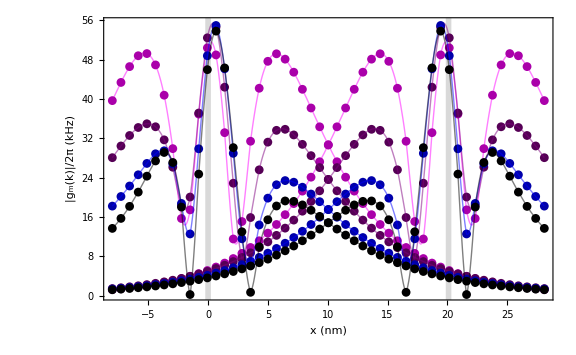

```mathematica
Colors={{Lighter[Red],Lighter[Red]},{Red,Red},{Darker[Red],Darker[Red]}};

cplot[i_]:=Show[Table[ListPlot[CouplingList[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[Darker[Blue],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"],{j,1,Length[CouplingList]}],ImageSize->Large,PlotRange->All,AspectRatio->1];

cplotsm[i_]:=Module[{TestEmptyList,v,plots},
TestEmptyList={};
Do[
Do[
AppendTo[TestEmptyList,CouplingList[[k]][[j]][[2]]]
,{j,1,Length[CouplingList[[k]]]}];
,{k,1,Length[CouplingList]}];

Do[

v=ListInterpolation[TestEmptyList[[Length[CouplingList[[j]]]*(j-1)+1;;Length[CouplingList[[j]]]*j]],{-8,N[l/a+20]*0.4}];
plot[j]=Plot[v[x],{x,-8,N[l/a+20]*0.4},LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"x (nm)","|g_m(k)|/2π (kHz)"},PlotStyle->Directive[Blue,Thick,Opacity[0.5]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,PlotLegends->Automatic]
,{j,1,Length[CouplingList]}];

plots=Show[Table[plot[j],{j,1,Length[CouplingList]}],ImageSize->Large,PlotRange->All,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]]];
plots

];

MANRKap2=cplot[1];
MANRKap2sm=cplotsm[1];
Show[MANRKap4sm,MANRKap4,MANRKap3,MANRKap3sm,MANRKap2,MANRKap2sm,MANRKap1,MANRKap1sm,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],AspectRatio->1/GoldenRatio]
```

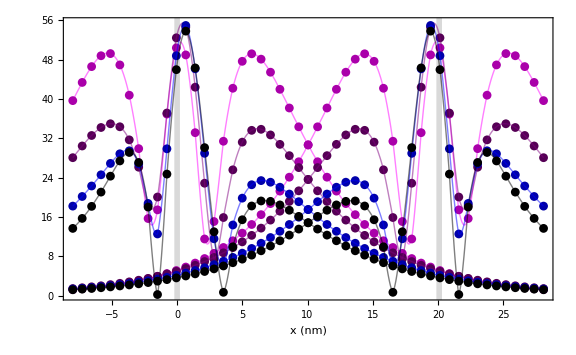

```mathematica
Show[-Graphics-,FrameStyle->Thick,FrameLabel->{"x (nm)",""}]
```

```mathematica
LineLegend[{Directive[Black,AbsoluteThickness[2],Opacity[0.5]],Directive[Blue,AbsoluteThickness[2],Opacity[0.5]],Directive[Purple,AbsoluteThickness[2],Opacity[0.5]],Directive[Magenta,AbsoluteThickness[2],Opacity[0.5]]},{"Δκ=0 (meV)","Δκ=0.1 (meV)","Δκ=0.2 (meV)","Δκ=0.3 (meV)"},LabelStyle->{FontFamily->"Cambria Math",FontSize->20},LegendMarkers->{Graphics[{Point[{0,0}],Black,Opacity[1]}],Graphics[{Point[{0,0}],Blue}],Graphics[{Point[{0,0}],Purple}],Graphics[{Point[{0,0}],Magenta}]},LegendMarkerSize->30]
```

```mathematica
(*
Write a function which finds the sup and inf bulk band structures at ka=0, also gives the band gap value.
*)
MinBulk[gap_,Num_,J_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_]:=
Module[{ξ,H,A,sortorder,EmptyList,lower,upper,L,U},
EmptyList={};
lower={};

ξ=0;
H=MANRMatrix2N[J,J2,DM,s,κ,Δκ,h,ϕ,ξ,Num];
A=Eigensystem[H];
sortorder=Ordering[A[[1]]];
f[ξ]=Table[{ξ ,(A[[1]][[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}];

For[i=1,f[0][[i]][[2]]<gap,i++,AppendTo[lower,f[0][[i]][[2]]]];

L=Max[lower];
U=f[0][[Length[lower]+3]][[2]];

AppendTo[EmptyList,{L,U,U-L}];

Flatten[EmptyList]

]
```

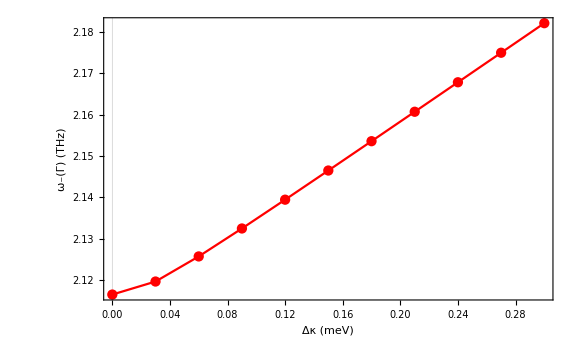

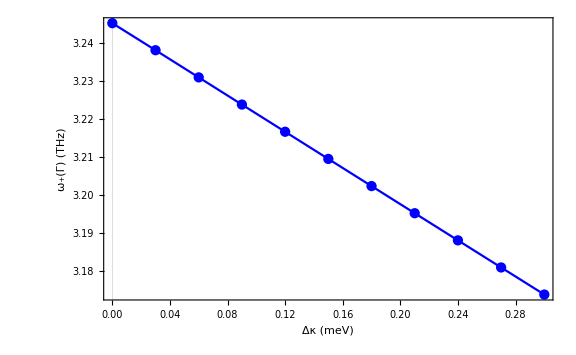

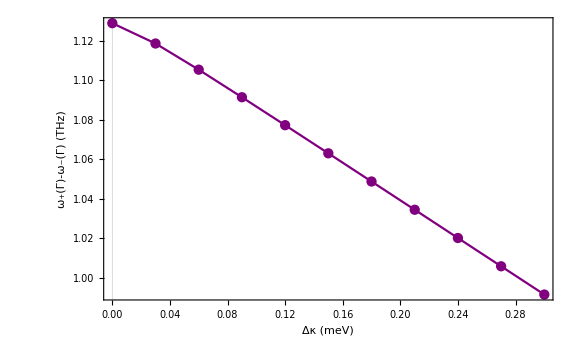

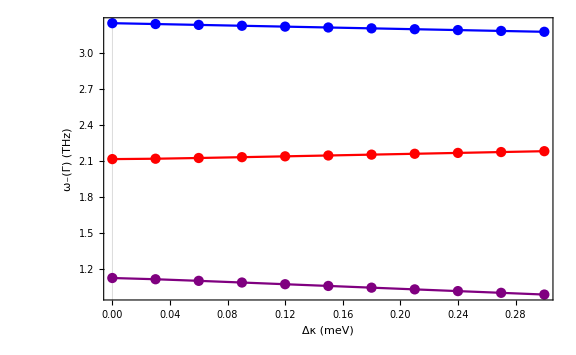

```mathematica
beepboopUP=ListPlot[Table[{Δκ,MinBulk[2.5,Num,J,J2,DM,s,κ,Δκ,h,ϕ][[1]]},{Δκ,0,0.3,0.03}],LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"Δκ (meV)","ω_-(Γ) (THz)"},PlotStyle->Directive[Red],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,AspectRatio->1/GoldenRatio];
beepboopUPsm=ListPlot[Table[{Δκ,MinBulk[2.5,Num,J,J2,DM,s,κ,Δκ,h,ϕ][[1]]},{Δκ,0,0.3,0.03}],LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"Δκ (meV)","ω_-(Γ) (THz)"},PlotStyle->Directive[Red],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,AspectRatio->1/GoldenRatio,Joined->True];
beepboopDN=ListPlot[Table[{Δκ,MinBulk[2.5,Num,J,J2,DM,s,κ,Δκ,h,ϕ][[2]]},{Δκ,0,0.3,0.03}],LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"Δκ (meV)","ω_+(Γ) (THz)"},PlotStyle->Directive[Blue],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,AspectRatio->1/GoldenRatio];
beepboopDNsm=ListPlot[Table[{Δκ,MinBulk[2.5,Num,J,J2,DM,s,κ,Δκ,h,ϕ][[2]]},{Δκ,0,0.3,0.03}],LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"Δκ (meV)","ω_+(Γ) (THz)"},PlotStyle->Directive[Blue],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,AspectRatio->1/GoldenRatio,Joined->True];
beepboopDIFF=ListPlot[Table[{Δκ,MinBulk[2.5,Num,J,J2,DM,s,κ,Δκ,h,ϕ][[3]]},{Δκ,0,0.3,0.03}],LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"Δκ (meV)","ω_+(Γ)-ω_-(Γ) (THz)"},PlotStyle->Directive[Purple],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,AspectRatio->1/GoldenRatio];
beepboopDIFFsm=ListPlot[Table[{Δκ,MinBulk[2.5,Num,J,J2,DM,s,κ,Δκ,h,ϕ][[3]]},{Δκ,0,0.3,0.03}],LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"Δκ (meV)","ω_+(Γ)-ω_-(Γ) (THz)"},PlotStyle->Directive[Purple],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,AspectRatio->1/GoldenRatio,Joined->True];
Show[beepboopUP,beepboopUPsm,PlotRange->All]
Show[beepboopDN,beepboopDNsm,PlotRange->All]
Show[beepboopDIFF,beepboopDIFFsm,PlotRange->All]
Show[beepboopUP,beepboopUPsm,beepboopDN,beepboopDNsm,beepboopDIFF,beepboopDIFFsm,PlotRange->All]
```

```mathematica
kap0=Import["C:\\Users\\jeffc\\Documents\\MANR-SCQ_full_strip_omega=3.1.mx"];
kap1=Import["MANR-SCQ_full_strip_omega=3.1_delkappa=0.1.mx"];
kap2=Import["MANR-SCQ_full_strip_omega=3.1_delkappa=0.2.mx"];
kap3=Import["MANR-SCQ_full_strip_omega=3.1_delkappa=0.3.mx"];
kap={kap0,kap1,kap2,kap3};

MANRKapCom=Table[Table[{kap[[j]][[1]][[i]][[1]],kap[[j]][[1]][[i]][[2]]+kap[[j]][[2]][[i]][[2]]},{i,1,Length[kap[[j]][[1]]]}],{j,1,Length[kap]}];
```

```mathematica
MANRKapCom[[2]]
```

{{-8.,19.5521},{-7.27816,21.6524},{-6.55633,23.942},{-5.83449,26.3987},{-5.11266,28.9062},{-4.39082,31.0791},{-3.66899,31.9291},{-2.94715,29.5366},{-2.22531,21.7903},{-1.50348,15.9126},{-0.781642,33.5989},{-0.0598063,52.9336},{0.662029,59.5457},{1.38387,51.2432},{2.1057,34.6169},{2.82754,17.8653},{3.54937,13.1654},{4.27121,22.1467},{4.99304,28.4696},{5.71488,32.148},{6.43672,34.0531},{7.15855,34.8882},{7.88039,35.1429},{8.60222,35.1365},{9.32406,35.0637},{10.0459,35.0285},{10.7677,35.0637},{11.4896,35.1365},{12.2114,35.1429},{12.9332,34.8882},{13.6551,34.0531},{14.3769,32.148},{15.0987,28.4696},{15.8206,22.1467},{16.5424,13.1654},{17.2643,17.8653},{17.9861,34.6169},{18.7079,51.2432},{19.4298,59.5457},{20.1516,52.9336},{20.8734,33.5989},{21.5953,15.9126},{22.3171,21.7903},{23.0389,29.5366},{23.7608,31.9291},{24.4826,31.0791},{25.2044,28.9062},{25.9263,26.3987},{26.6481,23.942},{27.37,21.6524},{28.0918,19.5521}}

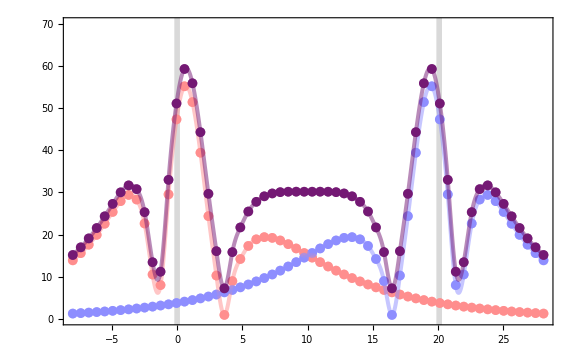

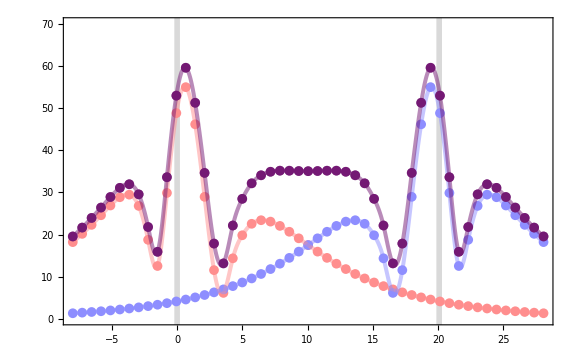

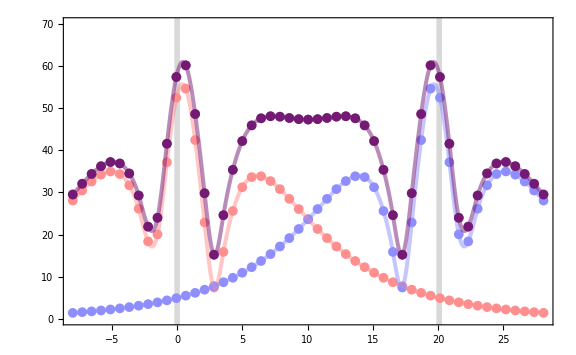

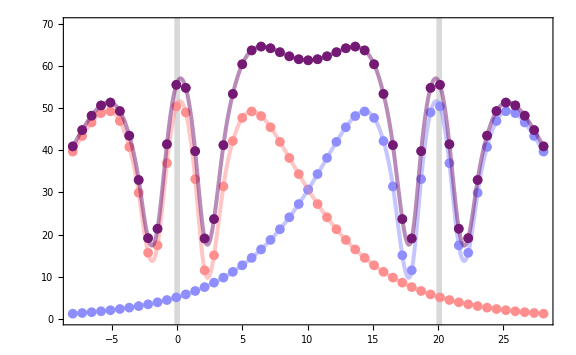

```mathematica
Colors={Blue,Red};

p0Com=Show[ListPlot[MANRKapCom[[1]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorData["GreenPinkTones",14/15],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],ImageSize->Large,PlotRange->{All,{0,70}}];
p0smoothCom=Show[ListPlot[MANRKapCom[[1]],Joined->True,InterpolationOrder->3,PlotRange->All,Joined->False,PlotStyle->Directive[ColorData["GreenPinkTones",14/15],Thickness[0.005],Opacity[0.5]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],ImageSize->Large,PlotRange->All];

p1Com=Show[ListPlot[MANRKapCom[[2]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorData["GreenPinkTones",14/15],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],ImageSize->Large,PlotRange->All];
p1smoothCom=Show[ListPlot[MANRKapCom[[2]],Joined->True,InterpolationOrder->3,PlotRange->All,PlotStyle->Directive[ColorData["GreenPinkTones",14/15],Thickness[0.005],Opacity[0.5]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],ImageSize->Large,PlotRange->All];

p2Com=Show[ListPlot[MANRKapCom[[3]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorData["GreenPinkTones",14/15],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],ImageSize->Large,PlotRange->All];
p2smoothCom=Show[ListPlot[MANRKapCom[[3]],Joined->True,InterpolationOrder->3,PlotRange->All,PlotStyle->Directive[ColorData["GreenPinkTones",14/15],Thickness[0.005],Opacity[0.5]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],ImageSize->Large,PlotRange->All];

p3Com=Show[ListPlot[MANRKapCom[[4]],PlotRange->All,Joined->False,PlotStyle->Directive[ColorData["GreenPinkTones",14/15],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],ImageSize->Large,PlotRange->All];
p3smoothCom=Show[ListPlot[MANRKapCom[[4]],Joined->True,InterpolationOrder->3,PlotRange->All,PlotStyle->Directive[ColorData["GreenPinkTones",14/15],Thickness[0.005],Opacity[0.5]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],ImageSize->Large,PlotRange->All];

plotcol={Directive[Lighter[Lighter[Red]],Thickness[0.005]],Directive[Lighter[Lighter[Blue]],Thickness[0.005]]};
plotcolopac={Directive[Lighter[Lighter[Red]],Thickness[0.005],Opacity[0.5]],Directive[Lighter[Lighter[Blue]],Thickness[0.005],Opacity[0.5]]};

p0=Show[Table[ListPlot[kap0[[j]],PlotRange->All,Joined->False,PlotStyle->plotcol[[j]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],{j,1,Length[kap0]}],ImageSize->Large,PlotRange->All];
p0smooth=Show[Table[ListPlot[kap0[[j]],Joined->True,InterpolationOrder->3,PlotRange->All,Joined->False,PlotStyle->plotcolopac[[j]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],{j,1,Length[kap0]}],ImageSize->Large,PlotRange->All];

p1=Show[Table[ListPlot[kap1[[j]],PlotRange->All,Joined->False,PlotStyle->plotcol[[j]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],{j,1,Length[kap1]}],ImageSize->Large,PlotRange->All];
p1smooth=Show[Table[ListPlot[kap1[[j]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->plotcolopac[[j]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"],{j,1,Length[kap1]}],ImageSize->Large,PlotRange->All];

p2=Show[Table[ListPlot[kap2[[j]],PlotRange->All,Joined->False,PlotStyle->plotcol[[j]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],{j,1,Length[kap2]}],ImageSize->Large,PlotRange->All];
p2smooth=Show[Table[ListPlot[kap2[[j]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->plotcolopac[[j]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"],{j,1,Length[kap2]}],ImageSize->Large,PlotRange->All];

p3=Show[Table[ListPlot[kap3[[j]],PlotRange->All,Joined->False,PlotStyle->plotcol[[j]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"",""},PlotTheme->"Scientific",PlotMarkers->{Automatic,Medium}],{j,1,Length[kap3]}],ImageSize->Large,PlotRange->All];
p3smooth=Show[Table[ListPlot[kap3[[j]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->plotcolopac[[j]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"],{j,1,Length[kap3]}],ImageSize->Large,PlotRange->All];


Show[p0,p0smooth,p0Com,p0smoothCom,PlotRange->{All,{0,70}},ImageSize->Large,FrameStyle->Thick,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],PlotMarkers->Automatic]
Show[p1,p1smooth,p1Com,p1smoothCom,PlotRange->{All,{0,70}},ImageSize->Large,FrameStyle->Thick,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],PlotMarkers->Automatic]
Show[p2,p2smooth,p2Com,p2smoothCom,PlotRange->{All,{0,70}},ImageSize->Large,FrameStyle->Thick,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],PlotMarkers->Automatic]
Show[p3,p3smooth,p3Com,p3smoothCom,PlotRange->{All,{0,70}},ImageSize->Large,FrameStyle->Thick,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]],PlotMarkers->Automatic]
```

## Maximum Coupling as a Function of Vertical Distance

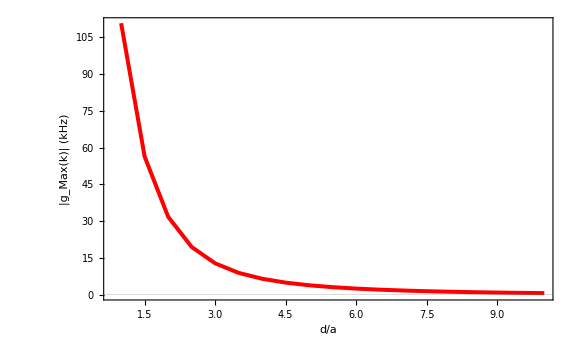

```mathematica
Num=50;
l=(√3)/2 2*Num*a;
F=γe*μ0*√((3μB Ms)/(2l w))*10^-3; (*KHz*)
ListPlot[Table[{r,F*MANRCoupling[J,J2,DM,s,κ,h,ϕ,-0.25,Num,Num,1.6,0,r]},{r,1,10,0.5}],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"d/a","|g_Max(k)| (kHz)"},PlotStyle->Directive[Red,Thickness[.005]],PlotTheme->"Scientific",Joined-> True,PlotRange->All,ImageSize->Large]
```

```mathematica
F*MANRCoupling[J,J2,DM,s,κ,h,ϕ,-0.25,Num,Num,1,0,1]
```

120.381

```mathematica
d=3;
Ek={{2.2,F*(MANRCoupling[J,J2,DM,s,κ,h,ϕ,-0.44,Num,Num,1,0,d]+MANRCoupling[J,J2,DM,s,κ,h,ϕ,0.44,Num,Num,1,0,d])},{2.4,F*(MANRCoupling[J,J2,DM,s,κ,h,ϕ,-0.25,Num,Num,1,0,d]+MANRCoupling[J,J2,DM,s,κ,h,ϕ,0.25,Num,Num,1,0,d])},{2.6,F*(MANRCoupling[J,J2,DM,s,κ,h,ϕ,-0.07,Num,Num,1,0,d]+MANRCoupling[J,J2,DM,s,κ,h,ϕ,0.07,Num,Num,1,0,d])},
{2.65,F*(MANRCoupling[J,J2,DM,s,κ,h,ϕ,0,Num,Num,1,0,d]+MANRCoupling[J,J2,DM,s,κ,h,ϕ,0,Num,Num,1,0,d])},
{2.7,F*(MANRCoupling[J,J2,DM,s,κ,h,ϕ,-0.03,Num,Num+1,1,0,d]+MANRCoupling[J,J2,DM,s,κ,h,ϕ,0.03,Num,Num+1,1,0,d])},
{2.8,F*(MANRCoupling[J,J2,DM,s,κ,h,ϕ,-0.13,Num,Num+1,1,0,d]+MANRCoupling[J,J2,DM,s,κ,h,ϕ,0.13,Num,Num+1,1,0,d])},{3,F*(MANRCoupling[J,J2,DM,s,κ,h,ϕ,-0.33,Num,Num+1,1,0,d]+MANRCoupling[J,J2,DM,s,κ,h,ϕ,0.33,Num,Num+1,1,0,d])}(*,
{3.2,F*(MANRCoupling[J,J2,DM,s,κ,h,ϕ,-0.6,Num,Num+1,1,0,d]+MANRCoupling[J,J2,DM,s,κ,h,ϕ,0.6,Num,Num+1,1,0,d])}*)};
```

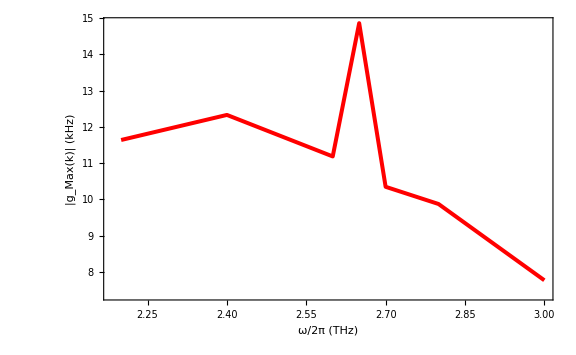

```mathematica
ListPlot[Ek,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->24}],FrameLabel->{"ω/2π (THz)","|g_Max(k)| (kHz)"},PlotStyle->Directive[Red,Thickness[.005]],PlotTheme->"Scientific",Joined-> True,PlotRange->All,ImageSize->Large]
```

```mathematica
F*(MANRCoupling[J,J2,DM,s,κ,h,ϕ,0,Num,Num+1,1,0,d]+MANRCoupling[J,J2,DM,s,κ,h,ϕ,0,Num,Num+1,1,0,d])
```

35.3669

```mathematica
Export["C:\\Users\\jeffc\\Downloads\\MANR-NV_gmax_vs_energy.png",%351,"PNG"]
```

C:\Users\jeffc\Downloads\MANR-NV_gmax_vs_energy.png

```mathematica
]
```

```mathematica
Export["C:\\Users\\jeffc\\Downloads\\MANR-NV_gmax_vs_k.png",%201,"PNG"]
```

C:\Users\jeffc\Downloads\MANR-NV_gmax_vs_k.png

## Impurities

### Functions

```mathematica
ImpureMANRMatrix2N[J1_,J2_,DM_,s_,κ_,h_,ϕ_,ξ_,N_]:=
Module[{H,N0=N,W,X,Y,Z},
H=ZeroMatrix2N[N0];

Quiet[Do[
H[[2+2(i-1)-1,2+2(i-1)]]=W;
H[[2+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,2+2(i-1)]]];

H[[3+2(i-1)-1,3+2(i-1)]]=X;
H[[3+2(i-1),3+2(i-1)-1]]=Conjugate[H[[3+2(i-1)-1,3+2(i-1)]]];
H[[2+2(i-1)-1,4+2(i-1)]]=Conjugate[X];
H[[4+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,4+2(i-1)]]];

H[[2+2(i-1)-1,3+2(i-1)]]=Y;
H[[3+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,3+2(i-1)]]];
H[[2+2(i-1),4+2(i-1)]]=Conjugate[Y];
H[[4+2(i-1),2+2(i-1)]]=Conjugate[H[[2+2(i-1),4+2(i-1)]]];

H[[2+2(i-1)-1,5+2(i-1)]]=Z;
H[[5+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,5+2(i-1)]]];
H[[2+2(i-1),6+2(i-1)]]=Conjugate[Z];
H[[6+2(i-1),2+2(i-1)]]=Conjugate[H[[2+2(i-1),6+2(i-1)]]];

H[[i,i]]=3 J1 s +6J2 s +h+(-1)^i κ;

W=-J1 s E^(ⅈ ξ);
X=-J1 s E^(ⅈ ξ/2);
Y=-2s √(DM^2+J2^2) E^(ⅈ ϕ) Cos[3/2 ξ];
Z=-s √(DM^2+J2^2)E^(-ⅈ ϕ);

,{i,1,2N0}];];

(*Edge effects*)
H[[1,1]]=H[[1,1]]-J1 s-3J2 s;
H[[2,2]]=H[[2,2]]-J1 s-3J2 s;
H[[3,3]]=H[[3,3]]-J2 s;
H[[4,4]]=H[[4,4]]-J2 s;
H[[2N0,2 N0]]=H[[2N0,2 N0]]-J1 s-3J2 s;
H[[2N0-1,2 N0-1]]=H[[2N0-1,2 N0-1]]-J1 s-3J2 s;
H[[2N0-2,2 N0-2]]=H[[2N0-2,2 N0-2]]-J2 s;
H[[2N0-3,2 N0-3]]=H[[2N0-3,2 N0-3]]-J2 s;

N0=N0+1;

(*Onsite impurity effects*)
H[[N0-1,N0-1]]=0;

H[[N0-2,N0-2]]=H[[N0-2,N0-2]]-J1 s;
H[[N0,N0]]=H[[N0,N0]]-J1 s;
H[[N0+2,N0+2]]=H[[N0+2,N0+2]]-J1 s;

H[[N0-5,N0-5]]=H[[N0-5,N0-5]]-J2 s;
H[[N0-3,N0-3]]=H[[N0-3,N0-3]]-2J2 s;
H[[N0+3,N0+3]]=H[[N0+3,N0+3]]-J2 s;
H[[N0+1,N0+1]]=H[[N0+1,N0+1]]-2J2 s;

(*NN Impurity effects*)
H[[N0-1,N0]]=H[[N0-1,N0]]+J1 s E^(ⅈ ξ);
H[[N0,N0-1]]=Conjugate[H[[N0-1,N0]]];
H[[N0-1,N0-2]]=H[[N0-1,N0-2]]+J1 s E^(-ⅈ ξ/2);
H[[N0-2,N0-1]]=Conjugate[H[[N0-1,N0-2]]];
H[[N0-1,N0+2]]=H[[N0-1,N0+2]]+J1 s E^(-ⅈ ξ/2);
H[[N0+2,N0-1]]=Conjugate[H[[N0-1,N0+2]]];


(*NNN Impurity effects*)
H[[N0-3,N0-1]]=H[[N0-3,N0-1]]+2s √(DM^2+J2^2) E^(ⅈ ϕ) Cos[3/2 ξ];
H[[N0-1,N0-3]]=Conjugate[H[[N0-3,N0-1]]];
H[[N0-1,N0+1]]=H[[N0-1,N0+1]]+2s √(DM^2+J2^2) E^(ⅈ ϕ) Cos[3/2 ξ];
H[[N0+1,N0-1]]=Conjugate[H[[N0-1,N0+1]]];
H[[N0-5,N0-1]]=H[[N0-5,N0-1]]+s √(DM^2+J2^2)E^(-ⅈ ϕ);
H[[N0-1,N0-5]]=Conjugate[H[[N0-5,N0-1]]];
H[[N0-1,N0+3]]=H[[N0-1,N0+3]]+s √(DM^2+J2^2)E^(-ⅈ ϕ);
H[[N0+3,N0-1]]=Conjugate[H[[N0-1,N0+3]]];

H
]


ImpureUMatrixMANR[J1_,J2_,DM_,s_,κ_,h_,ϕ_,ξ_,N_]:=
Module[{N0=N,H,sortorder,U},
H=ImpureMANRMatrix2N[J,J2,DM,s,κ,h,ϕ,ξ,N0];
sortorder=Ordering[Eigensystem[H][[1]]];
U=Chop[Eigensystem[H][[2]][[sortorder]]];
U
]

ImpureMANRCouplingDiscrete[J1_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,ξ_,Num_,m_,x_,y_,z_,sum1_,sum2_]:=
Module[{x1,y1,z1,x2,y2,z2,A,U,M,g,β,n},
x1=RecurrenceTable[{β[n+1]==β[n]+(√3)/2 KroneckerDelta[0,Mod[n,2]],β[1]==0},β,{n,1,2Num}];
U=ImpureUMatrixMANR[J1,J2,DM,s,κ,h,ϕ,ξ,Num];

g=(√3 3)/4 Norm[NIntegrate[Sum[(E^(ⅈ ξ)U[[m]][[M]]KroneckerDelta[Mod[M,4],1]+E^(-ⅈ ξ)U[[m]][[M]]KroneckerDelta[Mod[M,4],2]+E^(-ⅈ ξ/2)U[[m]][[M]]KroneckerDelta[Mod[M,4],3]+E^(ⅈ ξ/2)U[[m]][[M]]KroneckerDelta[Mod[M,4],0])*(-(3 (-x1[[M]]+x)^2)/(((-x1[[M]]+x)^2+(-y1+y)^2+(-z1+z)^2)^(5/2))+(3 (-y1+y)^2)/(((-x1[[M]]+x)^2+(-y1+y)^2+(-z1+z)^2)^(5/2)))E^(ⅈ ξ y1),{y1,sum1,sum2,3},{M,1,2Num}],{z1,-1/4,0},Method->{Automatic,"SymbolicProcessing"->0}]];

Chop[g]
]
```

### Dispersion

```mathematica
Naux=100;
Num=59;

Do[
ξ=-Pi/3+j* N[(2 Pi/3)/Naux];

H=ImpureMANRMatrix2N[J,J2,DM,s,κ,h,ϕ,ξ,Num];
sortorder=Ordering[Eigensystem[H][[1]]];

f[ξ]=Table[{ξ ,(Eigensystem[H][[1]][[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}];

,{j,0,Naux}]
```

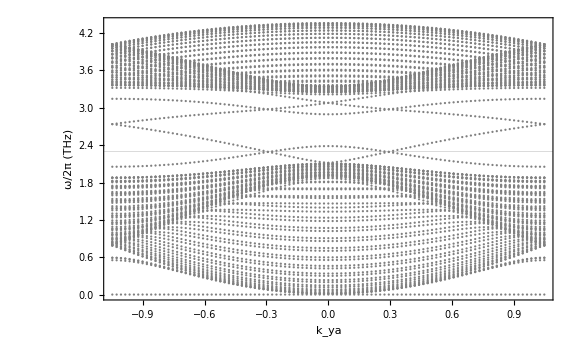

```mathematica
p=ListPlot[Table[f[ξ],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}],LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->48}],FrameLabel->{"k_ya","ω/2π (THz)"},FrameStyle->Thick,PlotStyle->Directive[Gray,Thickness[0.01]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Full];
p1=ListPlot[Table[f[ξ][[Num+2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}],LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"ka","ω (THz)"},PlotStyle->Directive[Blue,Thickness[.01]],PlotRange->All,PlotTheme->"Scientific"];p2=ListPlot[Table[f[ξ][[Num+1]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}],LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"ka","ω (THz)"},FrameStyle->Thick,PlotStyle->Directive[Red,Thickness[.01]],PlotRange->All,PlotTheme->"Scientific"];
Show[{p},ImageSize->Large,GridLines->{{},{2.3}},PlotRange->Full]
```

### Wavefunction Algorithm

```mathematica
(*(*Calculate table of values*)
Naux=200;
Num=59;
upperbound=3.4;
lowerbound=1.8;

Do[
ξ=-Pi/3+j* N[(2 Pi/3)/Naux];

H=ImpureMANRMatrix2N[J,J2,DM,s,κ,h,ϕ,ξ,Num];
sortorder=Ordering[Eigensystem[H][[1]]];

f[ξ]=Table[{ξ ,(Eigensystem[H][[1]][[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}];

,{j,0,Naux}];

(*Fun[l_]:=Table[f[ξ][[l]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}];*)

(*Iterates through table of values to grab indices which coincide to bands within desired bounds*)
FindIndices[Naux_,Num_,ub_,lb_]:=
Module[{EmptyList,Indices},
EmptyList={};

Do[
Do[
If[lb<Table[f[ξ][[i]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]]<ub, AppendTo[EmptyList,i]]
,{j,1,Length[Table[f[ξ][[i]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}]]}]
,{i,1,2Num}];

Indices=DeleteDuplicates[EmptyList];
Indices
];

BandIndices=FindIndices[Naux,Num,upperbound,lowerbound];

(*Find k value and corresponding band index for a fixed energy*)
FindMom[ω_,err_]:=
Module[{EmptyList,Mom},
EmptyList={};

Do[
Do[
If[ω-err<Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]]<ω+err, AppendTo[EmptyList,{BandIndices[[i]],Table[f[ξ][[BandIndices[[i]]]][[1]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]],Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]]}]]
,{j,1,Length[Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}]]}]
,{i,1,Length[BandIndices]}];

Mom=Sort[EmptyList,Abs[#1[[1]]]<Abs[#2[[1]]]&] (*Sorts list from smallest to largest absolute momentum*)
];

(*Takes the mean value of closely separated k values*)
MeanMom[ω_,err_]:=
Module[{MomList,DeleteMomList,EmptyList},

MomList=Split[FindMom[ω,err],Abs[#1[[2]]-#2[[2]]]<0.05&&#1[[1]]==#2[[1]]&];
EmptyList={};

For[i=1,i<Length[MomList]+1,i++,AppendTo[EmptyList,Mean[MomList[[i]]]]];

EmptyList
];

(*Calculates the wavefunction for impure spin lattice*)
wavefunctions[ω_,err_,Num_]:=
Module[{wavefunction,U,f,k,band,x,β,n},
wavefunction={};

Do[
k=MeanMom[ω,err][[j]][[2]];
band=MeanMom[ω,err][[j]][[1]];
U=ImpureUMatrixMANR[J,J2,DM,s,κ,h,ϕ,k,Num];
x=RecurrenceTable[{β[n+1]==β[n]+(√3)/2 KroneckerDelta[0,Mod[n,2]],β[1]==0},β,{n,1,2Num}];
f=Table[{x[[M]] a/10^-9,Abs[U[[band]][[M]]]^2},{M,1,2Num}];
AppendTo[wavefunction,f]
,{j,1,Length[MeanMom[ω,err]]}];

wavefunction

];
*)
```

```mathematica
(*Calculate table of values*)
(*κ=0.3;
Δκ=0.05;*)

Naux=100;
Num=59;

upperbound=3.4;
lowerbound=1.8;

WaveAlgoImpure[J_,J2_,DM_,s_,κ_,h_,ϕ_,Num_,Naux_,upperbound_,lowerbound_]:=
Module[{N0=Num,NBand=Naux,A},

Do[
ξ=-Pi/3+j* N[(2 Pi/3)/Naux];

H=ImpureMANRMatrix2N[J,J2,DM,s,κ,h,ϕ,ξ,Num];

A=Eigensystem[H];

sortorder=Ordering[A[[1]]];

f[ξ]=Table[{ξ ,(A[[1]][[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}];

,{j,0,Naux}];

(*Fun[l_]:=Table[f[ξ][[l]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}];*)

(*Iterates through table of values to grab indices which coincide to bands within desired bounds*)
FindIndicesImpure[NBand_,N0_,ub_,lb_]:=
Module[{EmptyList,Indices},
EmptyList={};

Do[
Do[
If[lb<Table[f[ξ][[i]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/NBand]}][[j]]<ub, AppendTo[EmptyList,i]]
,{j,1,Length[Table[f[ξ][[i]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/NBand]}]]}]
,{i,1,2N0}];

Indices=DeleteDuplicates[EmptyList];
Indices
];

BandIndices=FindIndicesImpure[Naux,Num,upperbound,lowerbound];

(*Find k value and corresponding band index for a fixed energy*)
FindMomImpure[ω_,err_]:=
Module[{EmptyList,Mom},
EmptyList={};

Do[
Do[
If[ω-err<Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]]<ω+err, AppendTo[EmptyList,{BandIndices[[i]],Table[f[ξ][[BandIndices[[i]]]][[1]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]],Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]]}]]
,{j,1,Length[Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}]]}]
,{i,1,Length[BandIndices]}];

Mom=Sort[EmptyList,Abs[#1[[1]]]<Abs[#2[[1]]]&] (*Sorts list from smallest to largest absolute momentum*)
];

(*Takes the mean value of closely separated k values*)
MeanMomImpure[ω_,err_]:=
Module[{MomList,DeleteMomList,EmptyList},

MomList=Split[FindMomImpure[ω,err],Abs[#1[[2]]-#2[[2]]]<0.05&&#1[[1]]==#2[[1]]&];
EmptyList={};

For[i=1,i<Length[MomList]+1,i++,AppendTo[EmptyList,Mean[MomList[[i]]]]];

EmptyList
];

(*Calculates the wavefunction for impure spin lattice*)
(*NOTE: I changed the x recurrence table to sum in steps of 1/2 instead of √3/2*)
ImpureWavefunctions[ω_,err_,N0]:=
Module[{wavefunction,U,f,k,band,β,n,x},
wavefunction={};

Do[
k=MeanMomImpure[ω,err][[j]][[2]];
band=MeanMomImpure[ω,err][[j]][[1]];
U=ImpureUMatrixMANR[J,J2,DM,s,κ,h,ϕ,k,Num];
x=RecurrenceTable[{β[n+1]==β[n]+(√3)/2 KroneckerDelta[0,Mod[n,2]],β[1]==0},β,{n,1,2Num}];
f=Table[{x[[M]] *a/10^-9,Abs[U[[band]][[M]]]^2},{M,1,2Num}];
AppendTo[wavefunction,f]
,{j,1,Length[MeanMomImpure[ω,err]]}];

wavefunction

];

];
```

### Plots

```mathematica
WaveAlgoImpure[J,J2,DM,s,κ,h,ϕ,Num,Naux,upperbound,lowerbound]
```

```mathematica
ImpWavs=ImpureWavefunctions[2.35,1/Naux,Num];
```

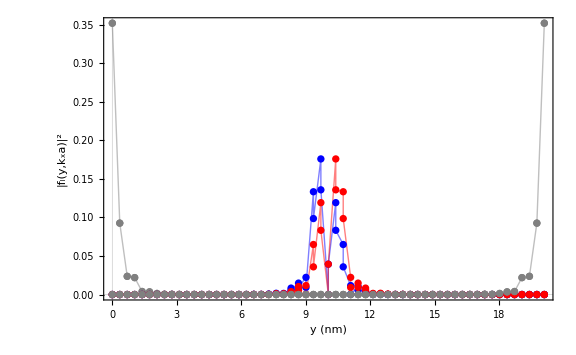

```mathematica
ColorListImp={Gray,Blue,Red,Gray};
imp1=Show[Table[ListPlot[ImpWavs[[j]],Joined->False,PlotRange->All,PlotStyle->Directive[ColorListImp[[j]],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[ImpWavs]}]];
imp1smooth=Show[Table[ListPlot[ImpWavs[[j]],Joined->True,PlotRange->All,PlotStyle->Directive[ColorListImp[[j]],Opacity[0.5],Thick],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","|f_l(y,k_xa)|^2"},PlotTheme->"Scientific"],{j,1,Length[ImpWavs]}]];
Show[imp1smooth,imp1,ImageSize->Large,PlotRange->All]
```

```mathematica
(*Plot that shit!*)
Wavefunctions=wavefunctions[2.4,0.01,Num];

TestEmptyList={};
Do[
Do[
AppendTo[TestEmptyList,Wavefunctions[[i]][[j]][[2]]]
,{j,1,Length[Wavefunctions[[i]]]}];
,{i,1,Length[Wavefunctions]}];

(*
Do[
v=ListInterpolation[TestEmptyList[[2Num*(j-1)+1;;2Num j]],{0,(√3)/2(Num-1)*0.4}];
plot[j]=Plot[v[x],{x,0,(√3)/2(Num-1)*0.4},LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"x (nm)","|f_y|^2"},PlotStyle->Directive[Green,Opacity[0.5],Thickness[0.005]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large]
,{j,1,Length[Wavefunctions]}];*)
```

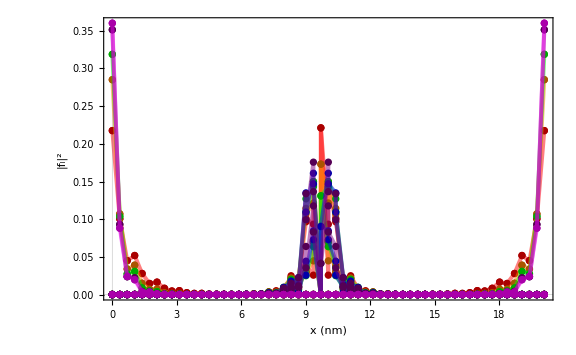

```mathematica
SmoothPlot=Table[ListPlot[Wavefunctions[[j]],PlotRange->All,Joined->True,PlotStyle->Directive[Magenta,Opacity[0.5],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"x (nm)","|f_l|^2"},PlotTheme->"Scientific"],{j,1,Length[Wavefunctions]}];
ChunkyPlot=Table[ListPlot[Wavefunctions[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[Darker[Magenta],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"x (nm)","|f_l|^2"},PlotTheme->"Scientific"],{j,1,Length[Wavefunctions]}];
impwav7=Show[SmoothPlot,ChunkyPlot,ImageSize->Large,PlotRange->All];

(*Show[impwav1,impwav2,impwav3,impwav4,impwav5,impwav6]*)
```

### Coupling

```mathematica
Num=59;
Naux=100;
WaveAlgoImpure[J,J2,DM,s,κ,h,ϕ,Num,Naux,upperbound,lowerbound];

NSteps=50;
ω=2.35;
error=0.01;

l=((√3)/2*(Num-1))*a;
(*l=3/2*2*Num*a;*)
d=12.5;
F=γe/(2Pi)*μ0/(√a)*√((3μB Ms)/(2l w))*10^-3; (*kHz*)

CouplingList={};

AbsoluteTiming[
Do[
numba=MeanMomImpure[ω,error][[j]][[1]];
mom=MeanMomImpure[ω,error][[j]][[2]];
Do[
x=-20+j*N[(l/a+40)/NSteps];
y=0;
gx=F*ImpureMANRCouplingDiscrete[J,J2,DM,s,κ,0,h,ϕ,mom,Num,numba,x,y,d,-3*200,3*200];
gm[x]={0.4*x,gx};
,{j,0,NSteps}];

AppendTo[CouplingList,Table[gm[x],{x,-20,l/a+20,N[(l/a+40)/NSteps]}]];

,{j,1,Length[MeanMom[ω,error]]}];
]
```

{1012.09,Null}

```mathematica
Export["MANR-SCQ_full_strip_omega=2.35_IMPURE.mx",CouplingList];
```

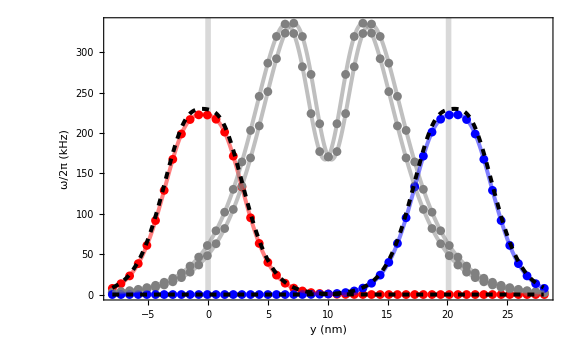

```mathematica
(*ImpColors={Gray,Red,Blue,Gray};*)
ImpColors={Red,Gray,Gray,Blue};
impcup=Show[Table[ListPlot[CouplingList[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[ImpColors[[j]],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"],{j,1,Length[CouplingList]}],ImageSize->Large,PlotRange->All];
impcupsmooth=Show[Table[ListPlot[CouplingList[[j]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[ImpColors[[j]],Opacity[0.5],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"],{j,1,Length[CouplingList]}],ImageSize->Large,PlotRange->All];

cup=Import["C:\\Users\\jeffc\\Documents\\MANR-SCQ_full_strip_omega=2.35.mx"];

cupPlotSmooth=Show[Table[ListPlot[cup[[j]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[Black,Dashed,Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"],{j,1,Length[cup]}],ImageSize->Large,PlotRange->All];
Show[impcup,impcupsmooth,cupPlotSmooth,PlotRange->All,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]]]
```

```mathematica
ImpColors={Gray,Lighter[Lighter[Red]],Lighter[Lighter[Blue]],Gray};
cupImp=Import["MANR-SCQ_full_strip_omega=2.35_IMPURE.mx"]

(*impcup=Show[Table[ListPlot[cupImp[[j]],PlotRange->All,Joined->False,PlotStyle->Directive[ImpColors[[j]],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"],{j,1,Length[cupImp]}],ImageSize->Large,PlotRange->All];
impcupsmooth=Show[Table[ListPlot[cupImp[[j]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[ImpColors[[j]],Opacity[0.5],Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"],{j,1,Length[cupImp]}],ImageSize->Large,PlotRange->All];

cup=Import["C:\\Users\\jeffc\\Documents\\MANR-SCQ_full_strip_omega=2.35.mx"];

cupPlotSmooth=Show[Table[ListPlot[cup[[j]],PlotRange->All,Joined->True,InterpolationOrder->3,PlotStyle->Directive[Black,Dashed,Thickness[0.005]],
LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->20}],FrameLabel->{"y (nm)","ω/2π (kHz)"},PlotTheme->"Scientific"],{j,1,Length[cup]}],ImageSize->Large,PlotRange->All];
Show[impcup,impcupsmooth,cupPlotSmooth,PlotRange->All,GridLines->{{0,N[l/a]*0.4},{}},GridLinesStyle->Directive[Thickness[0.007]]]*)
```

{}

# Workspace

```mathematica
Naux=200;
Num=59;

upperbound=3.2;
lowerbound=2.1;

WaveAlgoImpure[J_,J2_,DM_,s_,κ_,h_,ϕ_,Num_,Naux_,upperbound_,lowerbound_]:=Module[{N0=Num,NBand=Naux,A},fImpure[ξ_]:=Module[{H,sortorder,dumH},H=ImpureMANRMatrix2N[J,J2,DM,s,κ,h,ϕ,ξ,Num];
dumH=Eigenvalues[H];(*eigenvalues*)sortorder=Ordering[dumH];(*This orders the eigenvalues and eigenfunctions accordingly*)Table[{ξ,dumH[[sortorder]][[i]]/(2 Pi ℏ)},{i,1,2 Num}]];
ImpureDispersion=ParallelMap[fImpure,Table[-Pi/3+j*N[(2 Pi/3)/NSamp],{j,0,NSamp}]];
f[ξ_]:=Table[{Table[-Pi/3+j*N[(2 Pi/3)/Naux],{j,0,Naux}][[i]],ImpureDispersion[[i]]},{i,1,2 Num}];
(*Do[ξ=-Pi/3+j*N[(2 Pi/3)/Naux];
H=ImpureMANRMatrix2N[J,J2,DM,s,κ,h,ϕ,ξ,Num];
A=Eigenvalues[H];
sortorder=Ordering[A];
f[ξ]=Table[{ξ,A[[sortorder]][[i]]/(2 Pi ℏ)},{i,1,2 Num}];,{j,0,Naux}];*)(*Fun[l_]:=Table[f[ξ][[l]],{ξ,-(Pi/3),Pi/3,N[(2Pi/3)/Naux]}];*)(*Iterates through table of values to grab indices which coincide to bands within desired bounds*)FindIndicesImpure[NBand_,N0_,ub_,lb_]:=Module[{EmptyList,Indices,A2},EmptyList={};
Do[A2=Table[f[ξ][[i]][[2]],{ξ,-(Pi/3),Pi/3,N[(2 Pi/3)/NBand]}];
Do[If[lb<A2[[j]]<ub,AppendTo[EmptyList,i]],{j,1,Length[A2]}],{i,1,2 N0}];
Indices=DeleteDuplicates[EmptyList];
Indices];
BandIndices=FindIndicesImpure[Naux,Num,upperbound,lowerbound];
(*Find k value and corresponding band index for a fixed energy*)FindMomImpure[ω_,err_]:=Module[{EmptyList,Mom,A1,A2},EmptyList={};
Do[A1=Table[f[ξ][[BandIndices[[i]]]][[1]],{ξ,-(Pi/3),Pi/3,N[(2 Pi/3)/Naux]}];
A2=Table[f[ξ][[i]][[2]],{ξ,-(Pi/3),Pi/3,N[(2 Pi/3)/NBand]}];
Do[If[ω-err<A2[[j]]<ω+err,AppendTo[EmptyList,{BandIndices[[i]],A1[[j]],A2[[j]]}]],{j,1,Length[A2]}],{i,1,Length[BandIndices]}];
Mom=Sort[EmptyList,Abs[#1[[1]]]<Abs[#2[[1]]]&] (*Sorts list from smallest to largest absolute momentum*)];
(*Takes the mean value of closely separated k values*)MeanMomImpure[ω_,err_]:=Module[{MomList,DeleteMomList,EmptyList},MomList=Split[FindMomImpure[ω,err],Abs[#1[[2]]-#2[[2]]]<0.05&&#1[[1]]==#2[[1]]&];
EmptyList={};
For[i=1,i<Length[MomList]+1,i++,AppendTo[EmptyList,Mean[MomList[[i]]]]];
EmptyList];
(*Calculates the wavefunction for impure spin lattice*)(*NOTE:I changed the x recurrence table to sum in steps of 1/2 instead of Sqrt[3]/2*)ImpureWavefunctions[ω_,err_,N0]:=Module[{wavefunction,U,f,k,band,β,n,x},wavefunction={};
Do[k=MeanMomImpure[ω,err][[j]][[2]];
band=MeanMomImpure[ω,err][[j]][[1]];
U=ImpureUMatrixMANR[J,J2,DM,s,κ,h,ϕ,k,Num];
x=RecurrenceTable[{β[n+1]==β[n]+Sqrt[3]/2 KroneckerDelta[0,Mod[n,2]],β[1]==0},β,{n,1,2 Num}];
f=Table[{x[[M]]*a/10^-9,Abs[U[[band]][[M]]]^2},{M,1,2 Num}];
AppendTo[wavefunction,f],{j,1,Length[MeanMomImpure[ω,err]]}];
wavefunction];];
```

```mathematica
(*Calculate table of values*)
(*κ=0.3;
Δκ=0.05;*)

Naux=100;
Num=59;

upperbound=3.4;
lowerbound=1.8;

WaveAlgoImpure[J_,J2_,DM_,s_,κ_,h_,ϕ_,Num_,Naux_,upperbound_,lowerbound_]:=
Module[{N0=Num,NBand=Naux,A},

Do[
ξ=-Pi/3+j* N[(2 Pi/3)/Naux];

H=ImpureMANRMatrix2N[J,J2,DM,s,κ,h,ϕ,ξ,Num];

A=Eigensystem[H];

sortorder=Ordering[A[[1]]];

f[ξ]=Table[{ξ ,(A[[1]][[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}];

,{j,0,Naux}];

(*Fun[l_]:=Table[f[ξ][[l]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}];*)

(*Iterates through table of values to grab indices which coincide to bands within desired bounds*)
FindIndicesImpure[NBand_,N0_,ub_,lb_]:=
Module[{EmptyList,Indices,A2},
EmptyList={};

Do[
A2=Table[f[ξ][[i]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/NBand]}];
Do[
If[lb<A2[[j]]<ub, AppendTo[EmptyList,i]]
,{j,1,Length[A2]}]
,{i,1,2N0}];

Indices=DeleteDuplicates[EmptyList];
Indices
];

BandIndices=FindIndicesImpure[Naux,Num,upperbound,lowerbound];

(*Find k value and corresponding band index for a fixed energy*)
FindMomImpure[ω_,err_]:=
Module[{EmptyList,Mom,A1,A2},
EmptyList={};

Do[
A1=Table[f[ξ][[BandIndices[[i]]]][[1]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}];
A2=Table[f[ξ][[i]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/NBand]}];
Do[
If[ω-err<A2[[j]]<ω+err, AppendTo[EmptyList,{BandIndices[[i]],A1[[j]],A2[[j]]}]]
,{j,1,Length[A2]}]
,{i,1,Length[BandIndices]}];

Mom=Sort[EmptyList,Abs[#1[[1]]]<Abs[#2[[1]]]&] (*Sorts list from smallest to largest absolute momentum*)
];

(*Takes the mean value of closely separated k values*)
MeanMomImpure[ω_,err_]:=
Module[{MomList,DeleteMomList,EmptyList},

MomList=Split[FindMomImpure[ω,err],Abs[#1[[2]]-#2[[2]]]<0.05&&#1[[1]]==#2[[1]]&];
EmptyList={};

For[i=1,i<Length[MomList]+1,i++,AppendTo[EmptyList,Mean[MomList[[i]]]]];

EmptyList
];

(*Calculates the wavefunction for impure spin lattice*)
(*NOTE: I changed the x recurrence table to sum in steps of 1/2 instead of √3/2*)
ImpureWavefunctions[ω_,err_,N0]:=
Module[{wavefunction,U,f,k,band,β,n,x},
wavefunction={};

Do[
k=MeanMomImpure[ω,err][[j]][[2]];
band=MeanMomImpure[ω,err][[j]][[1]];
U=ImpureUMatrixMANR[J,J2,DM,s,κ,h,ϕ,k,Num];
x=RecurrenceTable[{β[n+1]==β[n]+(√3)/2 KroneckerDelta[0,Mod[n,2]],β[1]==0},β,{n,1,2Num}];
f=Table[{x[[M]] *a/10^-9,Abs[U[[band]][[M]]]^2},{M,1,2Num}];
AppendTo[wavefunction,f]
,{j,1,Length[MeanMomImpure[ω,err]]}];

wavefunction

];

];
```

```mathematica
MatrixForm[DyadG[x,y,z,x1,y1,z1]]
```

(-(3 (x-x1)^2)/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2))+1/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2)) | -(3 (x-x1) (y-y1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2)) | -(3 (x-x1) (z-z1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2))
-(3 (x-x1) (y-y1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2)) | -(3 (y-y1)^2)/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2))+1/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2)) | -(3 (y-y1) (z-z1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2))
-(3 (x-x1) (z-z1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2)) | -(3 (y-y1) (z-z1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2)) | 1/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2))-(3 (z-z1)^2)/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2)))

```mathematica
Do[
x=-5+j;
y=0;
z=12.5;
guh=Ms γe μ0 NIntegrate[Sum[Norm[(-(3 (x-x1) (z-z1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2))+ⅈ(-(3 (y-y1) (z-z1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2))))],{x1,0,20,1},{y1,-100,100}],{z1,-1/4,0}];
test[x]={x,guh}
,{j,0,30,1}]
```

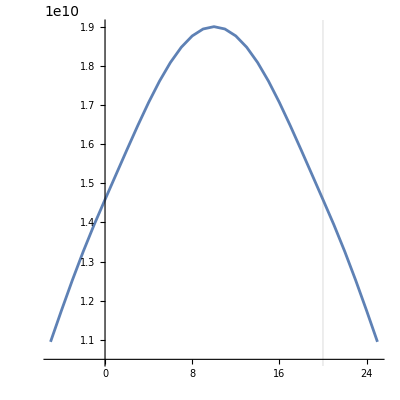

```mathematica
ListPlot[Table[test[x],{x,-5,25,1}],Joined->True,AspectRatio->1,GridLines->{{0,20},{}}]
```

```mathematica
2Num
```

40

```mathematica
(*Calculate table of values*)
Naux=300;
Num=20;
upperbound=3.4;
lowerbound=2;

Do[
ξ=-Pi/3+j* N[((2Pi)/3)/Naux];

H=ImpureMANRMatrix2N[J,J2,s,DM,h,κ,ξ,ϕ,Num];
sortorder=Ordering[Eigensystem[H][[1]]];

f[ξ]=Table[{ξ ,(Eigensystem[H][[1]][[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}];

,{j,0,Naux}]

(*Fun[l_]:=Table[f[ξ][[l]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}];*)

(*Iterates through table of values to grab indices which coincide to bands within desired bounds*)
(*FindIndices[Naux_,Num_,ub_,lb_]:=
Module[{EmptyList,Indices},
EmptyList={};

Do[
Do[
If[lb<Table[f[ξ][[i]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]]<ub, AppendTo[EmptyList,i]]
,{j,1,Length[Table[f[ξ][[i]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}]]}]
,{i,1,2Num}];

Indices=DeleteDuplicates[EmptyList];
Indices
];*)
```

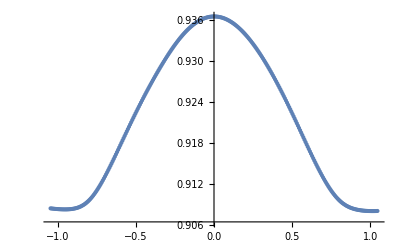

```mathematica
Fun[l_]:=Table[f[ξ][[l]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}];
ListPlot[Fun[2Num]]
```

```mathematica
Num=50;
l=(√3)/2 2*Num*a;
w=10^-11;(*m*)
d=5;
F=γe*μ0*√((3μB Ms)/(2l w))*10^3; (*KHz*)
N[l]*10^9
```

34.641

```mathematica
Clear[x,y,z];
A=DyadG[x,y,z,x1,y1,z1];
x=0;
y=0;
z=d;
A[[1]][[1]]+A[[2]][[2]]
```

-(3 x1^2)/((x1^2+y1^2+(5-z1)^2)^(5/2))-(3 y1^2)/((x1^2+y1^2+(5-z1)^2)^(5/2))+2/((x1^2+y1^2+(5-z1)^2)^(3/2))

$Aborted

ListPlot::lpn: {{{-1.0472,0.591178},{-1.0472,0.591178},{-1.0472,0.785614},{-1.0472,0.786485},{-1.0472,0.790909},{-«19»,«19»},{«1»},{-1.0472,0.807118},{-1.0472,0.813045},{-1.0472,0.824844},«108»},«9»,«491»} is not a list of numbers or pairs of numbers.